## Correlation functions in 4D CFT

```mathematica
Exit[]
```

This code is designed to completely automate the calculations for three-point correlation functions in 4D CFT. It is limited only by computer power, and has been explicitly tested up to spin-10.

Directions for using code:
1) Evaluate the “initialisation” block of code. This only needs to be evaluated once.
2) After inputting the spins in “2.1 - Parameters”, execute the entire block of code for 2.1.
3) Evaluate the “2.2 - Constraint analysis” block. This will automatically conserve the three-point function for the chosen spins. The results may be read off at each step in “results output”. To reset all variables, execute “Reset constraints”.

### 1 - Initialisation

#### 1.1 - Essential functions

The function below reduces a list of dependent structures down to a list of independent ones.

```mathematica
(* Sieve a list of structures *)
Indep[dep_][list_] := ((list//.dep//Expand)/.{Plus -> List}//Flatten)/.{_Integer A_ -> A}//DeleteDuplicates//Sort
SieveList[dep_][list_] := FixedPoint[ Indep[dep], list ]

(* Sieve an expression by applying linear dependence relations, expands until expression is fixed *)
ExprExpand[dep_][expr_] := expr/.dep//Expand
SieveExpr[dep_][expr_] := FixedPoint[ ExprExpand[dep], expr ]
```

Possible correlation functions for a given spin S:

```mathematica
nontrivialsol[S_] := Select[ 
Solve[ i1 + j1 + i2 + j2 + i3 + j3 == 2S && i1 ≤ i2 && i2 ≤ i3&& j1 ≤ j2 && j2 ≤ j3, {i1,j1,i2,j2,i3,j3}, NonNegativeIntegers ], 
EvenQ[ i1 + j1 + i2 + j2 + i3 + j3/.#]==True&];
```

The function below reads the index values off of the independent solutions. This is then fed into the derivative function.

```mathematica
indexvals[list_] := Table[Table[ vars[[i]] -> Exponent[list[[j]], invariants][[i]], {i,1,Length[vars]} ], {j,1,Length[list]}]
```

```mathematica
(* Weights of the fields in 4D *)
Spins := Table[ (Is[[i]] + Js[[i]])/2, {i, 1, Length[Is]} ]
overrideδ := If[ customδ == {}, {}, { Subscript[δ, 1] -> customδ[[1]], Subscript[δ, 2] -> customδ[[2]], Subscript[δ, 3] -> customδ[[3]] } ];
Δ := Table[ If[ Spins[[i]] == 0, Subscript[δ, i]/.overrideδ, If[ Spins[[i]] == 1/2, Subscript[δ, i]/.overrideδ, (Spins[[i]] + 2)], (Spins[[i]] + 2)], 
{i, 1, Length[Spins]}];

(* 1-2 parity functions for Abelian/non-Abelian currents) *)
parity12A := If[ OddQ[{Is[[1]] + Js[[1]], Is[[2]] + Js[[2]]}] == {True, True}, 1, 0 ];
parity12NA := If[ OddQ[{Is[[1]] + Js[[1]], Is[[2]] + Js[[2]]}] == {True, True}, 0, 1 ];

(* 1-2 parity function *)
parity12 := If[ Abelian == True, parity12A, parity12NA ];

(* Weights of the possible correlation tensors ansatz *)
q123 := Δ[[3]] - Δ[[2]] - Δ[[1]] ;
q213 := Δ[[2]] - Δ[[1]] - Δ[[3]] ;
q321 := Δ[[1]] - Δ[[2]] - Δ[[3]] ;

(* Specifies if the triangle inequality is obeyed, which allows us to optimise the code greatly *)
triangleinequalities := { Spins[[1]] ≤ Spins[[2]] + Spins[[3]], Spins[[2]] ≤ Spins[[1]] + Spins[[3]], Spins[[3]] ≤ Spins[[1]] + Spins[[2]] };
HS := triangleinequalities;

(* Conditions test for existence of 4D three-point function *)
Δs := 1/2(Is - Js)//Total
spinterval := {- Min[ Js[[1]] + Js[[2]], Js[[2]] + Js[[3]], Js[[1]] + Js[[3]] ], Min[ Is[[1]] + Is[[2]], Is[[2]] + Is[[3]], Is[[1]] + Is[[3]] ] }

(* Discriminant which seems to give identical results to the triangle inequalities;
If discriminant < 0, there are two even solutions and one odd solution, 
for discriminant ≥ 0, there are only two even solutions, the odd solution vanishes.  *)
ρ[ { s1_, s2_, s3_ } ] := ( s3 - s2 - s1 - 1 )( s1 - s2 - s3 - 1 )( s2 - s1 - s3 - 1 )//Expand
```

```mathematica
SolPane[ expr_, { xdim_, ratio_ } ] := 
Pane[ Style[expr//TraditionalForm, FontSize->20], ImageSize -> {xdim, UpTo[Round[ratio*xdim]]}, ImageSizeAction->"ShrinkToFit"]
```

#### 1.2 - Generating function code

This code needs to be evaluated once.

##### 1.2.1 - Building blocks I

Notation :
X is the coordinate vector in spinor notation, upper indices
Xl is the coordinate vector in spinor notation, lower indices
U, V, W are the undotted spinors with upper indices
Ul, Vl, Wl are the undotted spinors with lower indices
EPS is the epsilon tensor with upper undotted indices
EPSl is the epsilon tensor with lower undotted indices

```mathematica
(* epsilon tensors *)
d = 2;

EPS = Table[LeviCivitaTensor[2][[a, b]], {a,1,d},{b,1,d}];
EPSl = Table[-LeviCivitaTensor[2][[a, b]], {a,1,d},{b,1,d}];

eps = Table[LeviCivitaTensor[2][[a, b]], {a,1, d},{b,1, d}];
epsl = Table[-LeviCivitaTensor[2][[a, b]], {a,1, d},{b,1, d}];
```

```mathematica
(* undotted spinors *)
U = {U1, U2};
V = {V1, V2};
W = {W1, W2};
T = {T1, T2};

(* dotted spinors *)
u = {u1, u2};
v = {v1, v2};
w = {w1, w2};
t = {t1, t2};
```

```mathematica
(* undotted spinors with lower indices *)
Ul = Table[Sum[EPSl[[a, b]]U[[b]], {b,1,d}], {a, 1, d}];
Vl = Table[Sum[EPSl[[a, b]]V[[b]], {b,1,d}], {a, 1, d}];
Wl = Table[Sum[EPSl[[a, b]]W[[b]], {b,1,d}], {a, 1, d}];
Tl = Table[Sum[EPSl[[a, b]]T[[b]], {b,1,d}], {a, 1, d}];

(* dotted spinors with lower indices *)
ul = Table[Sum[epsl[[a, b]]u[[b]], {b,1,d}], {a, 1, d}];
vl = Table[Sum[epsl[[a, b]]v[[b]], {b,1,d}], {a, 1, d}];
wl = Table[Sum[epsl[[a, b]]w[[b]], {b,1,d}], {a, 1, d}];
tl = Table[Sum[epsl[[a, b]]t[[b]], {b,1,d}], {a, 1, d}];
```

```mathematica
(* building block vector *)
X = {{X11, X12}, {X21, X22}};
Xl = Table[Sum[EPSl[[a, p]] EPSl[[b, q]]X[[p, q]], {p,1,d}, {q,1,d}], {a, 1, d}, {b, 1, d}];

minusX = {X11 -> - X11, X12 -> - X12, X21 -> - X21, X22 -> - X22};
pointX = {X11 -> - X0 + X3, X12 -> X1 - I X2, X21 -> X1 + I X2, X22 -> - X0 - X3};
(* /.{ X0 -> 0, X1 -> 0, X2 -> 0, X3 -> 1} *)
```

Differential operators which act on explicit solutions for the generating function:

```mathematica
VXdt := (Sum[ V[[a]] hXl[[a,gd]]eps[[gd,ad]]D[#,t[[ad]]], {a,1,d}, {ad,1,d}, {gd,1,d}])&
vXdT := (Sum[ D[#,T[[a]]]EPS[[g,a]] hXl[[g,ad]]v[[ad]], {a,1, d}, {g,1,d}, {ad,1,d}])&

IVdt[k_] := 1/(k!)(Nest[VXdt,#,k])& 
IvdT[k_] := 1/(k!)(Nest[vXdT,#,k])&
```

Define the normalised three-point building blocks for convenience:

```mathematica
n[X_] := ( - 1/2 Sum[ EPS[[a,b]] eps[[ad,bd]]X[[a, ad]]X[[b,bd]], {a, 1, d}, {b, 1, d}, {ad, 1, d}, {bd, 1, d}]  )^(1/2) //Simplify
n[X]
n[X]/.pointX//Simplify
```

√(X12 X21-X11 X22)

√(-X0^2+X1^2+X2^2+X3^2)

```mathematica
hX = 1/n[X] X ;
hXl = 1/n[X] Xl ;
```

Now define the various possible polynomial basis structures and their replacement rules:

```mathematica
blocksub = { Subscript[P, 1] -> VW, Subscript[P, 2] -> WU, Subscript[P, 3] -> UV, Subscript[P̄, 1] -> vw, Subscript[P̄, 2] -> wu, Subscript[P̄, 3] -> uv, Subscript[Q, 1] -> VXw, Subscript[Q, 2] -> WXu, Subscript[Q, 3] -> UXv, Subscript[Q̄, 1] -> WXv, Subscript[Q̄, 2] -> UXw, Subscript[Q̄, 3] -> VXu, Subscript[Z, 1] -> UXu, Subscript[Z, 2] -> VXv, Subscript[Z, 3] -> WXw};
revblocksub = { VW -> Subscript[P, 1] , WU -> Subscript[P, 2], UV -> Subscript[P, 3], vw -> Subscript[P̄, 1], wu -> Subscript[P̄, 2], uv -> Subscript[P̄, 3], VXw -> Subscript[Q, 1], WXu -> Subscript[Q, 2], UXv -> Subscript[Q, 3], WXv -> Subscript[Q̄, 1], UXw -> Subscript[Q̄, 2], VXu -> Subscript[Q̄, 3], UXu -> Subscript[Z, 1], VXv -> Subscript[Z, 2], WXw -> Subscript[Z, 3]};
conjugatesol = { Subscript[P, 1] -> Subscript[P̄, 1] , Subscript[P, 2] -> Subscript[P̄, 2] , Subscript[P, 3] -> Subscript[P̄, 3] , Subscript[P̄, 1] -> Subscript[P, 1], Subscript[P̄, 2] -> Subscript[P, 2], Subscript[P̄, 3] -> Subscript[P, 3], Subscript[Q, 1] -> Subscript[Q̄, 1] , Subscript[Q, 2] -> Subscript[Q̄, 2] , Subscript[Q, 3] -> Subscript[Q̄, 3] , Subscript[Q̄, 1] -> Subscript[Q, 1], Subscript[Q̄, 2] -> Subscript[Q, 2], Subscript[Q̄, 3] -> Subscript[Q, 3], Subscript[Z, 1] -> Subscript[Z, 1], Subscript[Z, 2] -> Subscript[Z, 2], Subscript[Z, 3] -> Subscript[Z, 3]};

blockexpand = {
UV -> Sum[U[[c]] Vl[[c]], {c,1, d}],
WU -> Sum[W[[c]] Ul[[c]], {c,1, d}],
VW -> Sum[V[[c]] Wl[[c]], {c,1, d}],
uv -> Sum[u[[c]] vl[[c]], {c,1, d}],
wu -> Sum[w[[c]] ul[[c]], {c,1, d}],
vw -> Sum[v[[c]] wl[[c]], {c,1, d}],
UXv -> Sum[U[[a]] hXl[[a, b]]v[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
UXw -> Sum[U[[a]] hXl[[a, b]]w[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
VXu -> Sum[V[[a]]hXl[[a, b]] u[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
VXw -> Sum[V[[a]] hXl[[a, b]]w[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
WXu -> Sum[W[[a]] hXl[[a, b]] u[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
WXv -> Sum[W[[a]]hXl[[a, b]] v[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
UXu -> Sum[U[[a]] hXl[[a, b]] u[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
VXv -> Sum[V[[a]] hXl[[a, b]]v[[b]], {a,1, d}, {b,1, d}]/.pointX//Together,
WXw -> Sum[W[[a]] hXl[[a, b]] w[[b]], {a,1, d}, {b,1, d}]/.pointX//Together}

(* Spinor swaps, for more explicit computations *)
switch12spinors = {U1 -> V1, U2 -> V2, V1 -> U1, V2 -> U2, u1 -> v1, u2 -> v2, v1 -> u1, v2 -> u2};
switch13spinors = {U1 -> W1, U2 -> W2, W1 -> U1, W2 -> U2, u1 -> w1, u2 -> w2, w1 -> u1, w2 -> u2};
```

{UV→U2 V1-U1 V2,WU→-U2 W1+U1 W2,VW→V2 W1-V1 W2,uv→u2 v1-u1 v2,wu→-u2 w1+u1 w2,vw→v2 w1-v1 w2,UXv→(-U1 v1 X0-U2 v2 X0-U2 v1 X1-U1 v2 X1+ⅈ U2 v1 X2-ⅈ U1 v2 X2-U1 v1 X3+U2 v2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),UXw→(-U1 w1 X0-U2 w2 X0-U2 w1 X1-U1 w2 X1+ⅈ U2 w1 X2-ⅈ U1 w2 X2-U1 w1 X3+U2 w2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),VXu→(-u1 V1 X0-u2 V2 X0-u2 V1 X1-u1 V2 X1-ⅈ u2 V1 X2+ⅈ u1 V2 X2-u1 V1 X3+u2 V2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),VXw→(-V1 w1 X0-V2 w2 X0-V2 w1 X1-V1 w2 X1+ⅈ V2 w1 X2-ⅈ V1 w2 X2-V1 w1 X3+V2 w2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),WXu→(-u1 W1 X0-u2 W2 X0-u2 W1 X1-u1 W2 X1-ⅈ u2 W1 X2+ⅈ u1 W2 X2-u1 W1 X3+u2 W2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),WXv→(-v1 W1 X0-v2 W2 X0-v2 W1 X1-v1 W2 X1-ⅈ v2 W1 X2+ⅈ v1 W2 X2-v1 W1 X3+v2 W2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),UXu→(-u1 U1 X0-u2 U2 X0-U1 u2 X1-u1 U2 X1-ⅈ U1 u2 X2+ⅈ u1 U2 X2-u1 U1 X3+u2 U2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),VXv→(-v1 V1 X0-v2 V2 X0-V1 v2 X1-v1 V2 X1-ⅈ V1 v2 X2+ⅈ v1 V2 X2-v1 V1 X3+v2 V2 X3)/(√(-X0^2+X1^2+X2^2+X3^2)),WXw→(-w1 W1 X0-w2 W2 X0-W1 w2 X1-w1 W2 X1-ⅈ W1 w2 X2+ⅈ w1 W2 X2-w1 W1 X3+w2 W2 X3)/(√(-X0^2+X1^2+X2^2+X3^2))}

##### 1.2.2 - Building blocks II

“Primitive” linear dependence relations:

```mathematica
(* Subscript[Z, i] Subscript[P, i] relations *)
Subscript[Z, 1] Subscript[P, 1] + Subscript[P, 2] Subscript[Q̄, 3] + Subscript[P, 3] Subscript[Q, 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[P, 2] + Subscript[P, 3] Subscript[Q̄, 1] + Subscript[P, 1] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[P, 3] + Subscript[P, 1] Subscript[Q̄, 2] + Subscript[P, 2] Subscript[Q, 1] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[P̄, i] relations, conjugate of above *)
Subscript[Z, 1] Subscript[P̄, 1] + Subscript[P̄, 2] Subscript[Q, 3] + Subscript[P̄, 3] Subscript[Q̄, 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[P̄, 2] + Subscript[P̄, 3] Subscript[Q, 1] + Subscript[P̄, 1] Subscript[Q̄, 3] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[P̄, 3] + Subscript[P̄, 1] Subscript[Q, 2] + Subscript[P̄, 2] Subscript[Q̄, 1] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Q, i] relations *)
Subscript[Z, 1] Subscript[Q, 1] - Subscript[P̄, 2] Subscript[P, 3] - Subscript[Q̄, 2] Subscript[Q̄, 3] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[Q, 2] - Subscript[P̄, 3] Subscript[P, 1] - Subscript[Q̄, 3] Subscript[Q̄, 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[Q, 3] - Subscript[P̄, 1] Subscript[P, 2] - Subscript[Q̄, 1] Subscript[Q̄, 2] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Q̄, i] relations, conjugate of above *)
Subscript[Z, 1] Subscript[Q̄, 1] - Subscript[P, 2] Subscript[P̄, 3] - Subscript[Q, 2] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[Q̄, 2] - Subscript[P, 3] Subscript[P̄, 1] - Subscript[Q, 1] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[Q̄, 3] - Subscript[P, 1] Subscript[P̄, 2] - Subscript[Q, 1] Subscript[Q, 2] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Z, j] relations, self conjugate *)
Subscript[Z, 2] Subscript[Z, 3] + Subscript[P, 1] Subscript[P̄, 1] - Subscript[Q, 1] Subscript[Q̄, 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 1] Subscript[Z, 3] + Subscript[P, 2] Subscript[P̄, 2] - Subscript[Q, 2] Subscript[Q̄, 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 1] Subscript[Z, 2] + Subscript[P, 3] Subscript[P̄, 3] - Subscript[Q, 3] Subscript[Q̄, 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[P̄, i] Subscript[P, j] Subscript[Q̄, k] relations, self conjugate*)
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3] - Subscript[P, 1] Subscript[P̄, 2] Subscript[Q, 3] + Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] - Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1] - Subscript[P, 2] Subscript[P̄, 3] Subscript[Q, 1] + Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] - Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2] - Subscript[P, 3] Subscript[P̄, 1] Subscript[Q, 2] + Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] - Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[P, i] Subscript[P̄, j] Subscript[P̄, k] relations *)
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3] + Subscript[P̄, 1] Subscript[Q, 2] Subscript[Q̄, 3] + Subscript[P̄, 2] Subscript[Q̄, 3] Subscript[Q̄, 1] + Subscript[P̄, 3] Subscript[Q, 1] Subscript[Q, 2] /.blocksub/.blockexpand//Simplify;
Subscript[P, 2] Subscript[P̄, 3] Subscript[P̄, 1] + Subscript[P̄, 2] Subscript[Q, 3] Subscript[Q̄, 1] + Subscript[P̄, 3] Subscript[Q̄, 1] Subscript[Q̄, 2] + Subscript[P̄, 1] Subscript[Q, 2] Subscript[Q, 3] /.blocksub/.blockexpand//Simplify;
Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2] + Subscript[P̄, 3] Subscript[Q, 1] Subscript[Q̄, 2] + Subscript[P̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] + Subscript[P̄, 2] Subscript[Q, 3] Subscript[Q, 1] /.blocksub/.blockexpand//Simplify;

(* Subscript[P̄, i] Subscript[P, j] Subscript[P, k] relations, conjugate of above*)
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3] + Subscript[P, 1] Subscript[Q̄, 2] Subscript[Q, 3] + Subscript[P, 2] Subscript[Q, 3] Subscript[Q, 1] + Subscript[P, 3] Subscript[Q̄, 1] Subscript[Q̄, 2] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 2] Subscript[P, 3] Subscript[P, 1] + Subscript[P, 2] Subscript[Q̄, 3] Subscript[Q, 1] + Subscript[P, 3] Subscript[Q, 1] Subscript[Q, 2] + Subscript[P, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2] + Subscript[P, 3] Subscript[Q̄, 1] Subscript[Q, 2] + Subscript[P, 1] Subscript[Q, 2] Subscript[Q, 3] + Subscript[P, 2] Subscript[Q̄, 3] Subscript[Q̄, 1] /.blocksub/.blockexpand//Simplify;
```

```mathematica
(* We encode the linear dependence relations in the objects below *)
Subscript[(Z·P), 1] = - Subscript[P, 2] Subscript[Q̄, 3] - Subscript[P, 3] Subscript[Q, 2] ;
Subscript[(Z·P), 2] = - Subscript[P, 3] Subscript[Q̄, 1] - Subscript[P, 1] Subscript[Q, 3] ;
Subscript[(Z·P), 3] = - Subscript[P, 1] Subscript[Q̄, 2] - Subscript[P, 2] Subscript[Q, 1]  ;

Subscript[(Z·P̄), 1] = - Subscript[P̄, 2] Subscript[Q, 3] - Subscript[P̄, 3] Subscript[Q̄, 2] ;
Subscript[(Z·P̄), 2] = - Subscript[P̄, 3] Subscript[Q, 1] - Subscript[P̄, 1] Subscript[Q̄, 3] ;
Subscript[(Z·P̄), 3] = - Subscript[P̄, 1] Subscript[Q, 2] - Subscript[P̄, 2] Subscript[Q̄, 1] ;

Subscript[(Z·Q), 1] = Subscript[P̄, 2] Subscript[P, 3] + Subscript[Q̄, 2] Subscript[Q̄, 3] ;
Subscript[(Z·Q), 2] = Subscript[P̄, 3] Subscript[P, 1] + Subscript[Q̄, 3] Subscript[Q̄, 1] ;
Subscript[(Z·Q), 3] = Subscript[P̄, 1] Subscript[P, 2] + Subscript[Q̄, 1] Subscript[Q̄, 2] ;

Subscript[(Z·Q̄), 1] = Subscript[P, 2] Subscript[P̄, 3] + Subscript[Q, 2] Subscript[Q, 3] ;
Subscript[(Z·Q̄), 2] = Subscript[P, 3] Subscript[P̄, 1] + Subscript[Q, 3] Subscript[Q, 1] ;
Subscript[(Z·Q̄), 3] = Subscript[P, 1] Subscript[P̄, 2] + Subscript[Q, 1] Subscript[Q, 2] ;

Subscript[(Z·Z), 1] = - Subscript[P, 1] Subscript[P̄, 1] + Subscript[Q, 1] Subscript[Q̄, 1] ;
Subscript[(Z·Z), 2] = - Subscript[P, 2] Subscript[P̄, 2] + Subscript[Q, 2] Subscript[Q̄, 2] ;
Subscript[(Z·Z), 3] = - Subscript[P, 3] Subscript[P̄, 3] + Subscript[Q, 3] Subscript[Q̄, 3] ;

Subscript[(P̄·P·Q̄), 1] = Subscript[P, 1] Subscript[P̄, 2] Subscript[Q, 3] - Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] + Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] ;
Subscript[(P̄·P·Q̄), 2] = Subscript[P, 2] Subscript[P̄, 3] Subscript[Q, 1] - Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] + Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] ;
Subscript[(P̄·P·Q̄), 3] = Subscript[P, 3] Subscript[P̄, 1] Subscript[Q, 2] - Subscript[Q̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] + Subscript[Q, 1] Subscript[Q, 2] Subscript[Q, 3] ;

Subscript[(P·P̄·P̄), 1] = - Subscript[P̄, 1] Subscript[Q, 2] Subscript[Q̄, 3] - Subscript[P̄, 2] Subscript[Q̄, 3] Subscript[Q̄, 1] - Subscript[P̄, 3] Subscript[Q, 1] Subscript[Q, 2] ;
Subscript[(P·P̄·P̄), 2] = - Subscript[P̄, 2] Subscript[Q, 3] Subscript[Q̄, 1] - Subscript[P̄, 3] Subscript[Q̄, 1] Subscript[Q̄, 2] - Subscript[P̄, 1] Subscript[Q, 2] Subscript[Q, 3] ;
Subscript[(P·P̄·P̄), 3] = - Subscript[P̄, 3] Subscript[Q, 1] Subscript[Q̄, 2] - Subscript[P̄, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] - Subscript[P̄, 2] Subscript[Q, 3] Subscript[Q, 1] ;

Subscript[(P̄·P·P), 1] = - Subscript[P, 1] Subscript[Q̄, 2] Subscript[Q, 3] - Subscript[P, 2] Subscript[Q, 3] Subscript[Q, 1] - Subscript[P, 3] Subscript[Q̄, 1] Subscript[Q̄, 2] ;
Subscript[(P̄·P·P), 2] = - Subscript[P, 2] Subscript[Q̄, 3] Subscript[Q, 1] - Subscript[P, 3] Subscript[Q, 1] Subscript[Q, 2] - Subscript[P, 1] Subscript[Q̄, 2] Subscript[Q̄, 3] ;
Subscript[(P̄·P·P), 3] = - Subscript[P, 3] Subscript[Q̄, 1] Subscript[Q, 2] - Subscript[P, 1] Subscript[Q, 2] Subscript[Q, 3] - Subscript[P, 2] Subscript[Q̄, 3] Subscript[Q̄, 1] ;
```

```mathematica
(* Subscript[Z, i] Subscript[P, i] relations *)
Subscript[Z, 1] Subscript[P, 1] - Subscript[(Z·P), 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[P, 2] - Subscript[(Z·P), 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[P, 3] - Subscript[(Z·P), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[P̄, i] relations, conjugate of above *)
Subscript[Z, 1] Subscript[P̄, 1] - Subscript[(Z·P̄), 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[P̄, 2] - Subscript[(Z·P̄), 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[P̄, 3] - Subscript[(Z·P̄), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Q, i] relations *)
Subscript[Z, 1] Subscript[Q, 1] - Subscript[(Z·Q), 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[Q, 2] - Subscript[(Z·Q), 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[Q, 3] - Subscript[(Z·Q), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Q̄, i] relations, conjugate of above *)
Subscript[Z, 1] Subscript[Q̄, 1] - Subscript[(Z·Q̄), 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 2] Subscript[Q̄, 2] - Subscript[(Z·Q̄), 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 3] Subscript[Q̄, 3] - Subscript[(Z·Q̄), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[Z, i] Subscript[Z, j] relations, self conjugate *)
Subscript[Z, 2] Subscript[Z, 3] - Subscript[(Z·Z), 1] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 1] Subscript[Z, 3] - Subscript[(Z·Z), 2] /.blocksub/.blockexpand//Simplify;
Subscript[Z, 1] Subscript[Z, 2] - Subscript[(Z·Z), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[P̄, i] Subscript[P, j] Subscript[Q̄, k] relations, self conjugate*)
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3] - Subscript[(P̄·P·Q̄), 1] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1] - Subscript[(P̄·P·Q̄), 2] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2] - Subscript[(P̄·P·Q̄), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[P, i] Subscript[P̄, j] Subscript[P̄, k] relations *)
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3] - Subscript[(P·P̄·P̄), 1] /.blocksub/.blockexpand//Simplify;
Subscript[P, 2] Subscript[P̄, 3] Subscript[P̄, 1] - Subscript[(P·P̄·P̄), 2] /.blocksub/.blockexpand//Simplify;
Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2] - Subscript[(P·P̄·P̄), 3] /.blocksub/.blockexpand//Simplify;

(* Subscript[P̄, i] Subscript[P, j] Subscript[P, k] relations, conjugate of above*)
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3] - Subscript[(P̄·P·P), 1] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 2] Subscript[P, 3] Subscript[P, 1] - Subscript[(P̄·P·P), 2] /.blocksub/.blockexpand//Simplify;
Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2] - Subscript[(P̄·P·P), 3] /.blocksub/.blockexpand//Simplify;
```

```mathematica
(* Replacement rules for Z·P products *)
dep1 = {
Subscript[Z, 1] Subscript[P, 1] -> Subscript[(Z·P), 1], Subscript[Z, 2] Subscript[P, 2] -> Subscript[(Z·P), 2], Subscript[Z, 3] Subscript[P, 3] -> Subscript[(Z·P), 3],
Subscript[Z, 1] Subscript[P, 1]^A_ -> Subscript[P, 1]^(A-1) Subscript[(Z·P), 1], Subscript[Z, 2] Subscript[P, 2]^A_ -> Subscript[P, 2]^(A-1) Subscript[(Z·P), 2], Subscript[Z, 3] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1) Subscript[(Z·P), 3] , 
Subscript[Z, 1]^A_ Subscript[P, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·P), 1], Subscript[Z, 2]^A_ Subscript[P, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·P), 2], Subscript[Z, 3]^A_ Subscript[P, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·P), 3] , 
Subscript[Z, 1]^A_ Subscript[P, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[P, 1]^(B-Min[A,B]) Subscript[(Z·P), 1]^Min[A,B], Subscript[Z, 2]^A_ Subscript[P, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[P, 2]^(B-Min[A,B]) Subscript[(Z·P), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[P, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[P, 3]^(B-Min[A,B]) Subscript[(Z·P), 3]^Min[A,B] };

(* Replacement rules for Z·P̄ products *)
dep2 = {
Subscript[Z, 1] Subscript[P̄, 1] -> Subscript[(Z·P̄), 1], Subscript[Z, 2] Subscript[P̄, 2] -> Subscript[(Z·P̄), 2], Subscript[Z, 3] Subscript[P̄, 3] -> Subscript[(Z·P̄), 3],
Subscript[Z, 1] Subscript[P̄, 1]^A_ -> Subscript[P̄, 1]^(A-1) Subscript[(Z·P̄), 1], Subscript[Z, 2] Subscript[P̄, 2]^A_ -> Subscript[P̄, 2]^(A-1) Subscript[(Z·P̄), 2], Subscript[Z, 3] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1) Subscript[(Z·P̄), 3] , 
Subscript[Z, 1]^A_ Subscript[P̄, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·P̄), 1], Subscript[Z, 2]^A_ Subscript[P̄, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·P̄), 2], Subscript[Z, 3]^A_ Subscript[P̄, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·P̄), 3] , 
Subscript[Z, 1]^A_ Subscript[P̄, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[P̄, 1]^(B-Min[A,B]) Subscript[(Z·P̄), 1]^Min[A,B], Subscript[Z, 2]^A_ Subscript[P̄, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[P̄, 2]^(B-Min[A,B]) Subscript[(Z·P̄), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[P̄, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[P̄, 3]^(B-Min[A,B]) Subscript[(Z·P̄), 3]^Min[A,B] };

(* Replacement rules for Z·Q products *)
dep3 = {
Subscript[Z, 1] Subscript[Q, 1] -> Subscript[(Z·Q), 1] , Subscript[Z, 2] Subscript[Q, 2] -> Subscript[(Z·Q), 2] , Subscript[Z, 3] Subscript[Q, 3] -> Subscript[(Z·Q), 3],
Subscript[Z, 1] Subscript[Q, 1]^A_ -> Subscript[Q, 1]^(A-1) Subscript[(Z·Q), 1] , Subscript[Z, 2] Subscript[Q, 2]^A_ -> Subscript[Q, 2]^(A-1) Subscript[(Z·Q), 2], Subscript[Z, 3] Subscript[Q, 3]^A_ -> Subscript[Q, 3]^(A-1) Subscript[(Z·Q), 3], 
Subscript[Z, 1]^A_ Subscript[Q, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Q), 1] , Subscript[Z, 2]^A_ Subscript[Q, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Q), 2], Subscript[Z, 3]^A_ Subscript[Q, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·Q), 3], 
Subscript[Z, 1]^A_ Subscript[Q, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Q, 1]^(B-Min[A,B]) Subscript[(Z·Q), 1]^Min[A,B] , Subscript[Z, 2]^A_ Subscript[Q, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Q, 2]^(B-Min[A,B]) Subscript[(Z·Q), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[Q, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[Q, 3]^(B-Min[A,B]) Subscript[(Z·Q), 3]^Min[A,B] };

(* Replacement rules for Z·Q̄ products *)
dep4 = {
Subscript[Z, 1] Subscript[Q̄, 1] -> Subscript[(Z·Q̄), 1] , Subscript[Z, 2] Subscript[Q̄, 2] -> Subscript[(Z·Q̄), 2] , Subscript[Z, 3] Subscript[Q̄, 3] -> Subscript[(Z·Q̄), 3],
Subscript[Z, 1] Subscript[Q̄, 1]^A_ -> Subscript[Q̄, 1]^(A-1) Subscript[(Z·Q̄), 1] , Subscript[Z, 2] Subscript[Q̄, 2]^A_ -> Subscript[Q̄, 2]^(A-1) Subscript[(Z·Q̄), 2], Subscript[Z, 3] Subscript[Q̄, 3]^A_ -> Subscript[Q̄, 3]^(A-1) Subscript[(Z·Q̄), 3], 
Subscript[Z, 1]^A_ Subscript[Q̄, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Q̄), 1] , Subscript[Z, 2]^A_ Subscript[Q̄, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Q̄), 2], Subscript[Z, 3]^A_ Subscript[Q̄, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·Q̄), 3], 
Subscript[Z, 1]^A_ Subscript[Q̄, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Q̄, 1]^(B-Min[A,B]) Subscript[(Z·Q̄), 1]^Min[A,B] , Subscript[Z, 2]^A_ Subscript[Q̄, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Q̄, 2]^(B-Min[A,B]) Subscript[(Z·Q̄), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[Q̄, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[Q̄, 3]^(B-Min[A,B]) Subscript[(Z·Q̄), 3]^Min[A,B] };

(* Replacement rules for Z·Z products *)
dep5 = {
Subscript[Z, 2] Subscript[Z, 3] -> Subscript[(Z·Z), 1], Subscript[Z, 1] Subscript[Z, 3] -> Subscript[(Z·Z), 2], Subscript[Z, 1] Subscript[Z, 2] -> Subscript[(Z·Z), 3],
Subscript[Z, 2] Subscript[Z, 3]^A_ -> Subscript[Z, 3]^(A-1) Subscript[(Z·Z), 1], Subscript[Z, 1] Subscript[Z, 3]^A_ -> Subscript[Z, 3]^(A-1) Subscript[(Z·Z), 2], Subscript[Z, 1] Subscript[Z, 2]^A_ -> Subscript[Z, 2]^(A-1) Subscript[(Z·Z), 3],
Subscript[Z, 2]^A_ Subscript[Z, 3] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Z), 1], Subscript[Z, 1]^A_ Subscript[Z, 3] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Z), 2], Subscript[Z, 1]^A_ Subscript[Z, 2] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Z), 3],
Subscript[Z, 2]^A_ Subscript[Z, 3]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Z, 3]^(B-Min[A,B]) Subscript[(Z·Z), 1]^Min[A,B] , Subscript[Z, 1]^A_ Subscript[Z, 3]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Z, 3]^(B-Min[A,B]) Subscript[(Z·Z), 2]^Min[A,B], Subscript[Z, 1]^A_ Subscript[Z, 2]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Z, 2]^(B-Min[A,B]) Subscript[(Z·Z), 3]^Min[A,B]};

(* Replacement rules for Q·P·P̄ product *)
dep6 = { 
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3] -> Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1] -> Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2] -> Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[Q̄, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2]^A_ Subscript[P, 3] Subscript[Q̄, 1] -> Subscript[P̄, 2]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[Q̄, 2] -> Subscript[P̄, 3]^(A-1)Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[Q̄, 3] -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3]^A_ Subscript[Q̄, 1] -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[Q̄, 2] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3]^A_ -> Subscript[Q̄, 3]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1]^A_ -> Subscript[Q̄, 1]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2]^A_ -> Subscript[Q̄, 2]^(A-1)Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[Q̄, 3] -> Subscript[P̄, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2]^A_ Subscript[P, 3]^B_ Subscript[Q̄, 1] -> Subscript[P̄, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[Q̄, 2] -> Subscript[P̄, 3]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·Q̄), 3]^1,
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[Q̄, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[Q̄, 3]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2]^A_ Subscript[P, 3] Subscript[Q̄, 1]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[Q̄, 1]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[Q̄, 2]^B_ -> Subscript[P̄, 3]^(A-1) Subscript[Q̄, 2]^(B-1)Subscript[(P̄·P·Q̄), 3]^1,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[Q̄, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[Q̄, 3]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2] Subscript[P, 3]^A_ Subscript[Q̄, 1]^B_ -> Subscript[P, 3]^(A-1) Subscript[Q̄, 1]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[Q̄, 2]^B_ -> Subscript[P, 1]^(A-1) Subscript[Q̄, 2]^(B-1)Subscript[(P̄·P·Q̄), 3]^1,
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[Q̄, 3]^C_ -> Subscript[P̄, 1]^(A-Min[A,B,C]) Subscript[P, 2]^(B-Min[A,B,C]) Subscript[Q̄, 3]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 1]^Min[A,B,C], Subscript[P̄, 2]^A_ Subscript[P, 3]^B_ Subscript[Q̄, 1]^C_ -> Subscript[P̄, 2]^(A-Min[A,B,C]) Subscript[P, 3]^(B-Min[A,B,C]) Subscript[Q̄, 1]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 2]^Min[A,B,C], Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[Q̄, 2]^C_ -> Subscript[P̄, 3]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[Q̄, 2]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 3]^Min[A,B,C]} ; 

(* Replacement rules for P·P̄·P̄ product *)
dep7 = { 
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3] -> Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1] Subscript[P̄, 3] -> Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2] -> Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1]^A_ Subscript[P̄, 2] Subscript[P̄, 3] -> Subscript[P, 1]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2]^A_ Subscript[P̄, 1] Subscript[P̄, 3] -> Subscript[P, 2]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3]^A_ Subscript[P̄, 1] Subscript[P̄, 2] -> Subscript[P, 3]^(A-1)Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1] Subscript[P̄, 2]^A_ Subscript[P̄, 3] -> Subscript[P̄, 2]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1]^A_ Subscript[P̄, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1]^A_ Subscript[P̄, 2] -> Subscript[P̄, 1]^(A-1)Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2]^A_ -> Subscript[P̄, 2]^(A-1)Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1]^A_ Subscript[P̄, 2]^B_ Subscript[P̄, 3] -> Subscript[P, 1]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 3] -> Subscript[P, 2]^(A-1) Subscript[P̄, 1]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 2] -> Subscript[P, 3]^(A-1) Subscript[P̄, 1]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,
Subscript[P, 1]^A_ Subscript[P̄, 2] Subscript[P̄, 3]^B_ -> Subscript[P, 1]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2]^A_ Subscript[P̄, 1] Subscript[P̄, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3]^A_ Subscript[P̄, 1] Subscript[P̄, 2]^B_ -> Subscript[P, 3]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,
Subscript[P, 1] Subscript[P̄, 2]^A_ Subscript[P̄, 3]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2] Subscript[P̄, 1]^A_ Subscript[P̄, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3] Subscript[P̄, 1]^A_ Subscript[P̄, 2]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,
Subscript[P, 1]^A_ Subscript[P̄, 2]^B_ Subscript[P̄, 3]^C_ -> Subscript[P, 1]^(A-Min[A,B,C]) Subscript[P̄, 2]^(B-Min[A,B,C]) Subscript[P̄, 3]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 1]^Min[A,B,C], Subscript[P, 2]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 3]^C_ -> Subscript[P, 2]^(A-Min[A,B,C]) Subscript[P̄, 1]^(B-Min[A,B,C]) Subscript[P̄, 3]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 2]^Min[A,B,C] , Subscript[P, 3]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 2]^C_ -> Subscript[P, 3]^(A-Min[A,B,C]) Subscript[P̄, 1]^(B-Min[A,B,C]) Subscript[P̄, 2]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 3]^Min[A,B,C] } ; 

(* Replacement rules for P̄·P·P product *)
dep8 = { 
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3] -> Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1] Subscript[P, 3] -> Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2] -> Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[P, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2]^A_ Subscript[P, 1] Subscript[P, 3] -> Subscript[P̄, 2]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[P, 2] -> Subscript[P̄, 3]^(A-1)Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[P, 3] -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1]^A_ Subscript[P, 3] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[P, 2] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2]^A_ -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[P, 3] -> Subscript[P̄, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2]^A_ Subscript[P, 1]^B_ Subscript[P, 3] -> Subscript[P̄, 2]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[P, 2] -> Subscript[P̄, 3]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·P), 3]^1 ,
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[P, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2]^A_ Subscript[P, 1] Subscript[P, 3]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[P, 2]^B_ -> Subscript[P̄, 3]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 3]^1 ,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[P, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2] Subscript[P, 1]^A_ Subscript[P, 3]^B_ -> Subscript[P, 1]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[P, 2]^B_ -> Subscript[P, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 3]^1 ,
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[P, 3]^C_ -> Subscript[P̄, 1]^(A-Min[A,B,C]) Subscript[P, 2]^(B-Min[A,B,C]) Subscript[P, 3]^(C-Min[A,B,C])Subscript[(P̄·P·P), 1]^Min[A,B,C] , Subscript[P̄, 2]^A_ Subscript[P, 1]^B_ Subscript[P, 3]^C_ -> Subscript[P̄, 2]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[P, 3]^(C-Min[A,B,C])Subscript[(P̄·P·P), 2]^Min[A,B,C] , Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[P, 2]^C_ -> Subscript[P̄, 3]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[P, 2]^(C-Min[A,B,C])Subscript[(P̄·P·P), 3]^Min[A,B,C]  } ; 

dep = Join[ dep1, dep2, dep3, dep4, dep5, dep6, dep7, dep8 ];
```

Same thing except sorted differently, need to test timing:

```mathematica
dep3A = { 
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[Q̄, 3]^C_ -> Subscript[P̄, 1]^(A-Min[A,B,C]) Subscript[P, 2]^(B-Min[A,B,C]) Subscript[Q̄, 3]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 1]^Min[A,B,C], Subscript[P̄, 2]^A_ Subscript[P, 3]^B_ Subscript[Q̄, 1]^C_ -> Subscript[P̄, 2]^(A-Min[A,B,C]) Subscript[P, 3]^(B-Min[A,B,C]) Subscript[Q̄, 1]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 2]^Min[A,B,C], Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[Q̄, 2]^C_ -> Subscript[P̄, 3]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[Q̄, 2]^(C-Min[A,B,C])Subscript[(P̄·P·Q̄), 3]^Min[A,B,C],
Subscript[P, 1]^A_ Subscript[P̄, 2]^B_ Subscript[P̄, 3]^C_ -> Subscript[P, 1]^(A-Min[A,B,C]) Subscript[P̄, 2]^(B-Min[A,B,C]) Subscript[P̄, 3]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 1]^Min[A,B,C], Subscript[P, 2]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 3]^C_ -> Subscript[P, 2]^(A-Min[A,B,C]) Subscript[P̄, 1]^(B-Min[A,B,C]) Subscript[P̄, 3]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 2]^Min[A,B,C] , Subscript[P, 3]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 2]^C_ -> Subscript[P, 3]^(A-Min[A,B,C]) Subscript[P̄, 1]^(B-Min[A,B,C]) Subscript[P̄, 2]^(C-Min[A,B,C])Subscript[(P·P̄·P̄), 3]^Min[A,B,C],
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[P, 3]^C_ -> Subscript[P̄, 1]^(A-Min[A,B,C]) Subscript[P, 2]^(B-Min[A,B,C]) Subscript[P, 3]^(C-Min[A,B,C])Subscript[(P̄·P·P), 1]^Min[A,B,C] , Subscript[P̄, 2]^A_ Subscript[P, 1]^B_ Subscript[P, 3]^C_ -> Subscript[P̄, 2]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[P, 3]^(C-Min[A,B,C])Subscript[(P̄·P·P), 2]^Min[A,B,C], Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[P, 2]^C_ -> Subscript[P̄, 3]^(A-Min[A,B,C]) Subscript[P, 1]^(B-Min[A,B,C]) Subscript[P, 2]^(C-Min[A,B,C])Subscript[(P̄·P·P), 3]^Min[A,B,C]};

dep3B = {
Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[P, 3] -> Subscript[P̄, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2]^A_ Subscript[P, 1]^B_ Subscript[P, 3] -> Subscript[P̄, 2]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[P, 2] -> Subscript[P̄, 3]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·P), 3]^1 ,
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[P, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2]^A_ Subscript[P, 1] Subscript[P, 3]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[P, 2]^B_ -> Subscript[P̄, 3]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 3]^1 ,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[P, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 1]^1 , Subscript[P̄, 2] Subscript[P, 1]^A_ Subscript[P, 3]^B_ -> Subscript[P, 1]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·P), 2]^1 , Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[P, 2]^B_ -> Subscript[P, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·P), 3]^1 ,

Subscript[P, 1]^A_ Subscript[P̄, 2]^B_ Subscript[P̄, 3] -> Subscript[P, 1]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 3] -> Subscript[P, 2]^(A-1) Subscript[P̄, 1]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3]^A_ Subscript[P̄, 1]^B_ Subscript[P̄, 2] -> Subscript[P, 3]^(A-1) Subscript[P̄, 1]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,
Subscript[P, 1]^A_ Subscript[P̄, 2] Subscript[P̄, 3]^B_ -> Subscript[P, 1]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2]^A_ Subscript[P̄, 1] Subscript[P̄, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3]^A_ Subscript[P̄, 1] Subscript[P̄, 2]^B_ -> Subscript[P, 3]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,
Subscript[P, 1] Subscript[P̄, 2]^A_ Subscript[P̄, 3]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 1]^1, Subscript[P, 2] Subscript[P̄, 1]^A_ Subscript[P̄, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P̄, 3]^(B-1)Subscript[(P·P̄·P̄), 2]^1 , Subscript[P, 3] Subscript[P̄, 1]^A_ Subscript[P̄, 2]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[P̄, 2]^(B-1)Subscript[(P·P̄·P̄), 3]^1 ,

Subscript[P̄, 1]^A_ Subscript[P, 2]^B_ Subscript[Q̄, 3] -> Subscript[P̄, 1]^(A-1) Subscript[P, 2]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2]^A_ Subscript[P, 3]^B_ Subscript[Q̄, 1] -> Subscript[P̄, 2]^(A-1) Subscript[P, 3]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3]^A_ Subscript[P, 1]^B_ Subscript[Q̄, 2] -> Subscript[P̄, 3]^(A-1) Subscript[P, 1]^(B-1)Subscript[(P̄·P·Q̄), 3]^1,
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[Q̄, 3]^B_ -> Subscript[P̄, 1]^(A-1) Subscript[Q̄, 3]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2]^A_ Subscript[P, 3] Subscript[Q̄, 1]^B_ -> Subscript[P̄, 2]^(A-1) Subscript[Q̄, 1]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[Q̄, 2]^B_ -> Subscript[P̄, 3]^(A-1) Subscript[Q̄, 2]^(B-1)Subscript[(P̄·P·Q̄), 3]^1,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[Q̄, 3]^B_ -> Subscript[P, 2]^(A-1) Subscript[Q̄, 3]^(B-1)Subscript[(P̄·P·Q̄), 1]^1, Subscript[P̄, 2] Subscript[P, 3]^A_ Subscript[Q̄, 1]^B_ -> Subscript[P, 3]^(A-1) Subscript[Q̄, 1]^(B-1)Subscript[(P̄·P·Q̄), 2]^1, Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[Q̄, 2]^B_ -> Subscript[P, 1]^(A-1) Subscript[Q̄, 2]^(B-1)Subscript[(P̄·P·Q̄), 3]^1 };

dep3C = {
Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[P, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2]^A_ Subscript[P, 1] Subscript[P, 3] -> Subscript[P̄, 2]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[P, 2] -> Subscript[P̄, 3]^(A-1)Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[P, 3] -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1]^A_ Subscript[P, 3] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[P, 2] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·P), 3] ,
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2]^A_ -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·P), 3] ,

Subscript[P, 1]^A_ Subscript[P̄, 2] Subscript[P̄, 3] -> Subscript[P, 1]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2]^A_ Subscript[P̄, 1] Subscript[P̄, 3] -> Subscript[P, 2]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3]^A_ Subscript[P̄, 1] Subscript[P̄, 2] -> Subscript[P, 3]^(A-1)Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1] Subscript[P̄, 2]^A_ Subscript[P̄, 3] -> Subscript[P̄, 2]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1]^A_ Subscript[P̄, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1]^A_ Subscript[P̄, 2] -> Subscript[P̄, 1]^(A-1)Subscript[(P·P̄·P̄), 3] ,
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1)Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1)Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2]^A_ -> Subscript[P̄, 2]^(A-1)Subscript[(P·P̄·P̄), 3] ,

Subscript[P̄, 1]^A_ Subscript[P, 2] Subscript[Q̄, 3] -> Subscript[P̄, 1]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2]^A_ Subscript[P, 3] Subscript[Q̄, 1] -> Subscript[P̄, 2]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3]^A_ Subscript[P, 1] Subscript[Q̄, 2] -> Subscript[P̄, 3]^(A-1)Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1] Subscript[P, 2]^A_ Subscript[Q̄, 3] -> Subscript[P, 2]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3]^A_ Subscript[Q̄, 1] -> Subscript[P, 3]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1]^A_ Subscript[Q̄, 2] -> Subscript[P, 1]^(A-1)Subscript[(P̄·P·Q̄), 3],
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3]^A_ -> Subscript[Q̄, 3]^(A-1)Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1]^A_ -> Subscript[Q̄, 1]^(A-1)Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2]^A_ -> Subscript[Q̄, 2]^(A-1)Subscript[(P̄·P·Q̄), 3] };

dep3D = {
Subscript[P̄, 1] Subscript[P, 2] Subscript[Q̄, 3] -> Subscript[(P̄·P·Q̄), 1], Subscript[P̄, 2] Subscript[P, 3] Subscript[Q̄, 1] -> Subscript[(P̄·P·Q̄), 2], Subscript[P̄, 3] Subscript[P, 1] Subscript[Q̄, 2] -> Subscript[(P̄·P·Q̄), 3] ,
Subscript[P, 1] Subscript[P̄, 2] Subscript[P̄, 3] -> Subscript[(P·P̄·P̄), 1] , Subscript[P, 2] Subscript[P̄, 1] Subscript[P̄, 3] -> Subscript[(P·P̄·P̄), 2] , Subscript[P, 3] Subscript[P̄, 1] Subscript[P̄, 2] -> Subscript[(P·P̄·P̄), 3] ,
Subscript[P̄, 1] Subscript[P, 2] Subscript[P, 3] -> Subscript[(P̄·P·P), 1] , Subscript[P̄, 2] Subscript[P, 1] Subscript[P, 3] -> Subscript[(P̄·P·P), 2] , Subscript[P̄, 3] Subscript[P, 1] Subscript[P, 2] -> Subscript[(P̄·P·P), 3] };

dep2A = {
Subscript[Z, 2]^A_ Subscript[Z, 3]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Z, 3]^(B-Min[A,B]) Subscript[(Z·Z), 1]^Min[A,B] , Subscript[Z, 1]^A_ Subscript[Z, 3]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Z, 3]^(B-Min[A,B]) Subscript[(Z·Z), 2]^Min[A,B], Subscript[Z, 1]^A_ Subscript[Z, 2]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Z, 2]^(B-Min[A,B]) Subscript[(Z·Z), 3]^Min[A,B],
Subscript[Z, 1]^A_ Subscript[Q̄, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Q̄, 1]^(B-Min[A,B]) Subscript[(Z·Q̄), 1]^Min[A,B] , Subscript[Z, 2]^A_ Subscript[Q̄, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Q̄, 2]^(B-Min[A,B]) Subscript[(Z·Q̄), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[Q̄, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[Q̄, 3]^(B-Min[A,B])Subscript[(Z·Q̄), 3]^Min[A,B],
Subscript[Z, 1]^A_ Subscript[Q, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[Q, 1]^(B-Min[A,B]) Subscript[(Z·Q), 1]^Min[A,B] , Subscript[Z, 2]^A_ Subscript[Q, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[Q, 2]^(B-Min[A,B]) Subscript[(Z·Q), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[Q, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[Q, 3]^(B-Min[A,B]) Subscript[(Z·Q), 3]^Min[A,B],
Subscript[Z, 1]^A_ Subscript[P̄, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[P̄, 1]^(B-Min[A,B]) Subscript[(Z·P̄), 1]^Min[A,B], Subscript[Z, 2]^A_ Subscript[P̄, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[P̄, 2]^(B-Min[A,B]) Subscript[(Z·P̄), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[P̄, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[P̄, 3]^(B-Min[A,B]) Subscript[(Z·P̄), 3]^Min[A,B],
Subscript[Z, 1]^A_ Subscript[P, 1]^B_ -> Subscript[Z, 1]^(A-Min[A,B]) Subscript[P, 1]^(B-Min[A,B]) Subscript[(Z·P), 1]^Min[A,B], Subscript[Z, 2]^A_ Subscript[P, 2]^B_ -> Subscript[Z, 2]^(A-Min[A,B]) Subscript[P, 2]^(B-Min[A,B]) Subscript[(Z·P), 2]^Min[A,B], Subscript[Z, 3]^A_ Subscript[P, 3]^B_ -> Subscript[Z, 3]^(A-Min[A,B]) Subscript[P, 3]^(B-Min[A,B]) Subscript[(Z·P), 3]^Min[A,B] };

dep2B = {
Subscript[Z, 1] Subscript[P, 1]^A_ -> Subscript[P, 1]^(A-1) Subscript[(Z·P), 1], Subscript[Z, 2] Subscript[P, 2]^A_ -> Subscript[P, 2]^(A-1) Subscript[(Z·P), 2], Subscript[Z, 3] Subscript[P, 3]^A_ -> Subscript[P, 3]^(A-1) Subscript[(Z·P), 3] , 
Subscript[Z, 1]^A_ Subscript[P, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·P), 1], Subscript[Z, 2]^A_ Subscript[P, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·P), 2], Subscript[Z, 3]^A_ Subscript[P, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·P), 3] , 

Subscript[Z, 1] Subscript[P̄, 1]^A_ -> Subscript[P̄, 1]^(A-1) Subscript[(Z·P̄), 1], Subscript[Z, 2] Subscript[P̄, 2]^A_ -> Subscript[P̄, 2]^(A-1) Subscript[(Z·P̄), 2], Subscript[Z, 3] Subscript[P̄, 3]^A_ -> Subscript[P̄, 3]^(A-1) Subscript[(Z·P̄), 3] , 
Subscript[Z, 1]^A_ Subscript[P̄, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·P̄), 1], Subscript[Z, 2]^A_ Subscript[P̄, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·P̄), 2], Subscript[Z, 3]^A_ Subscript[P̄, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·P̄), 3] , 

Subscript[Z, 1] Subscript[Q, 1]^A_ -> Subscript[Q, 1]^(A-1) Subscript[(Z·Q), 1] , Subscript[Z, 2] Subscript[Q, 2]^A_ -> Subscript[Q, 2]^(A-1) Subscript[(Z·Q), 2], Subscript[Z, 3] Subscript[Q, 3]^A_ -> Subscript[Q, 3]^(A-1) Subscript[(Z·Q), 3], 
Subscript[Z, 1]^A_ Subscript[Q, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Q), 1] , Subscript[Z, 2]^A_ Subscript[Q, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Q), 2], Subscript[Z, 3]^A_ Subscript[Q, 3] -> Subscript[Z, 3]^(A-1) Subscript[(Z·Q), 3], 

Subscript[Z, 1] Subscript[Q̄, 1]^A_ -> Subscript[Q̄, 1]^(A-1) Subscript[(Z·Q̄), 1] , Subscript[Z, 2] Subscript[Q̄, 2]^A_ -> Subscript[Q̄, 2]^(A-1) Subscript[(Z·Q̄), 2], Subscript[Z, 3] Subscript[Q̄, 3]^A_ -> Subscript[Q̄, 3]^(A-1)Subscript[(Z·Q̄), 3], 
Subscript[Z, 1]^A_ Subscript[Q̄, 1] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Q̄), 1] , Subscript[Z, 2]^A_ Subscript[Q̄, 2] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Q̄), 2], Subscript[Z, 3]^A_ Subscript[Q̄, 3] -> Subscript[Z, 3]^(A-1)Subscript[(Z·Q̄), 3], 

Subscript[Z, 2] Subscript[Z, 3]^A_ -> Subscript[Z, 3]^(A-1) Subscript[(Z·Z), 1], Subscript[Z, 1] Subscript[Z, 3]^A_ -> Subscript[Z, 3]^(A-1) Subscript[(Z·Z), 2], Subscript[Z, 1] Subscript[Z, 2]^A_ -> Subscript[Z, 2]^(A-1) Subscript[(Z·Z), 3],
Subscript[Z, 2]^A_ Subscript[Z, 3] -> Subscript[Z, 2]^(A-1) Subscript[(Z·Z), 1], Subscript[Z, 1]^A_ Subscript[Z, 3] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Z), 2], Subscript[Z, 1]^A_ Subscript[Z, 2] -> Subscript[Z, 1]^(A-1) Subscript[(Z·Z), 3] };

dep2C = {
Subscript[Z, 1] Subscript[P, 1] -> Subscript[(Z·P), 1], Subscript[Z, 2] Subscript[P, 2] -> Subscript[(Z·P), 2], Subscript[Z, 3] Subscript[P, 3] -> Subscript[(Z·P), 3],
Subscript[Z, 1] Subscript[P̄, 1] -> Subscript[(Z·P̄), 1], Subscript[Z, 2] Subscript[P̄, 2] -> Subscript[(Z·P̄), 2], Subscript[Z, 3] Subscript[P̄, 3] -> Subscript[(Z·P̄), 3],
Subscript[Z, 1] Subscript[Q, 1] -> Subscript[(Z·Q), 1], Subscript[Z, 2] Subscript[Q, 2] -> Subscript[(Z·Q), 2] , Subscript[Z, 3] Subscript[Q, 3] -> Subscript[(Z·Q), 3],
Subscript[Z, 1] Subscript[Q̄, 1] -> Subscript[(Z·Q̄), 1], Subscript[Z, 2] Subscript[Q̄, 2] -> Subscript[(Z·Q̄), 2], Subscript[Z, 3] Subscript[Q̄, 3] -> Subscript[(Z·Q̄), 3],
Subscript[Z, 2] Subscript[Z, 3] -> Subscript[(Z·Z), 1], Subscript[Z, 1] Subscript[Z, 3] -> Subscript[(Z·Z), 2], Subscript[Z, 1] Subscript[Z, 2] -> Subscript[(Z·Z), 3] };

dep2 = Join[ dep3A, dep2A, dep3B, dep3C, dep3D, dep2B, dep2C ];
```

Now define various replacement rules which act on the generating function for point switch identities.

```mathematica
(* Recall that under 1 <-> 2 exchange, u <-> v, U <-> V, X -> - X *)
switch12 = { 
Subscript[P, 1] -> - Subscript[P, 2], Subscript[P, 2] -> - Subscript[P, 1], Subscript[P, 3] -> - Subscript[P, 3], 
Subscript[P̄, 1] -> - Subscript[P̄, 2], Subscript[P̄, 2] -> - Subscript[P̄, 1], Subscript[P̄, 3] -> - Subscript[P̄, 3], 
Subscript[Q, 1] -> - Subscript[Q̄, 2], Subscript[Q, 2] -> - Subscript[Q̄, 1], Subscript[Q, 3] -> - Subscript[Q̄, 3], 
Subscript[Q̄, 1] -> - Subscript[Q, 2], Subscript[Q̄, 2] -> - Subscript[Q, 1], Subscript[Q̄, 3] -> - Subscript[Q, 3], 
Subscript[Z, 1] -> - Subscript[Z, 2], Subscript[Z, 2] -> - Subscript[Z, 1], Subscript[Z, 3] -> - Subscript[Z, 3] };

(* Recall that under 1 <-> 3 exchange, u <-> w, U <-> W, X -> - X *)
switch13 = { 
Subscript[P, 1] -> - Subscript[P, 3], Subscript[P, 2] -> - Subscript[P, 2], Subscript[P, 3] -> - Subscript[P, 1], 
Subscript[P̄, 1] -> - Subscript[P̄, 3], Subscript[P̄, 2] -> - Subscript[P̄, 2], Subscript[P̄, 3] -> - Subscript[P̄, 1], 
Subscript[Q, 1] -> - Subscript[Q̄, 3], Subscript[Q, 2] -> - Subscript[Q̄, 2], Subscript[Q, 3] -> - Subscript[Q̄, 1], 
Subscript[Q̄, 1] -> - Subscript[Q, 3], Subscript[Q̄, 2] -> - Subscript[Q, 2], Subscript[Q̄, 3] -> - Subscript[Q, 1], 
Subscript[Z, 1] -> - Subscript[Z, 3], Subscript[Z, 2] -> - Subscript[Z, 2], Subscript[Z, 3] -> - Subscript[Z, 1] };

(* This operator computes Htilde from H *)
D13 = { 
Subscript[P, 1] -> - Subscript[Q̄, 1], Subscript[P, 2] -> Subscript[P, 2], Subscript[P, 3] -> Subscript[Q, 3], 
Subscript[P̄, 1] -> - Subscript[Q, 1], Subscript[P̄, 2] -> Subscript[P̄, 2], Subscript[P̄, 3] -> Subscript[Q̄, 3], 
Subscript[Q, 1] -> - Subscript[P̄, 1], Subscript[Q, 2] -> Subscript[Q, 2], Subscript[Q, 3] -> Subscript[P, 3], 
Subscript[Q̄, 1] -> - Subscript[P, 1], Subscript[Q̄, 2] -> Subscript[Q̄, 2], Subscript[Q̄, 3] -> Subscript[P̄, 3], 
Subscript[Z, 1] -> Subscript[Z, 1], Subscript[Z, 2] -> - Subscript[Z, 2], Subscript[Z, 3] -> Subscript[Z, 3] };

(* Inversion transformation *)
invertstructures = { 
Subscript[P, 1] -> - Subscript[P̄, 1], Subscript[P, 2] -> - Subscript[P̄, 2], Subscript[P, 3] -> - Subscript[P̄, 3], 
Subscript[P̄, 1] -> - Subscript[P, 1], Subscript[P̄, 2] -> - Subscript[P, 2], Subscript[P̄, 3] -> - Subscript[P, 3], 
Subscript[Q, 1] -> - Subscript[Q̄, 1], Subscript[Q, 2] -> - Subscript[Q̄, 2], Subscript[Q, 3] -> - Subscript[Q̄, 3], 
Subscript[Q̄, 1] -> - Subscript[Q, 1], Subscript[Q̄, 2] -> - Subscript[Q, 2], Subscript[Q̄, 3] -> - Subscript[Q, 3], 
Subscript[Z, 1] -> - Subscript[Z, 1], Subscript[Z, 2] -> - Subscript[Z, 2], Subscript[Z, 3] -> - Subscript[Z, 3] };
```

Transformation rules for Htilde:

```mathematica
Table[ invariants[[i]] -> (invariants/.invertstructures/.D13)[[i]], {i, 1, Length[invariants]} ]
```

{}

##### 1.2.3 - Generating function

Define the constants which represent homogeneities of the various building blocks:

```mathematica
K = Table[Subscript[k, i], {i,1,3}];
K̄ = Table[Subscript[k̄ ,i], {i,1,3}];

L = Table[Subscript[l, i], {i,1,3}];
L̄ = Table[Subscript[l̄ ,i], {i,1,3}];

M = Table[ Subscript[m,i], {i,1,3}];

vars = Join[ K , K̄ , L , L̄ , M]
```

{k_1,k_2,k_3,(k̄)_1,(k̄)_2,(k̄)_3,l_1,l_2,l_3,(l̄)_1,(l̄)_2,(l̄)_3,m_1,m_2,m_3}

Construct the generating polynomial from the building blocks:

```mathematica
Ps = {Subscript[P, 1], Subscript[P, 2], Subscript[P, 3]};
Pbs = {Subscript[P̄, 1], Subscript[P̄, 2], Subscript[P̄, 3]};
Qs = {Subscript[Q, 1], Subscript[Q, 2], Subscript[Q, 3]};
Qbs = {Subscript[Q̄, 1], Subscript[Q̄, 2], Subscript[Q̄, 3]};
Zs = {Subscript[Z, 1], Subscript[Z, 2], Subscript[Z, 3]};
invariants = Join[ Ps, Pbs, Qs, Qbs, Zs ];

σ[I_, c_] := Subscript[I, 1]^c[[1]] Subscript[I, 2]^c[[2]] Subscript[I, 3]^c[[3]]
F[P_, Q_, Z_] := σ[P, K]σ[P̄, K̄]σ[Q, L]σ[Q̄, L̄]σ[Z, M];
```

```mathematica
F[P,Q,Z]
```

P_1^k_1 P_2^k_2 P_3^k_3 Q_1^l_1 Q_2^l_2 Q_3^l_3 Z_1^m_1 Z_2^m_2 Z_3^m_3 (P̄)_1^((k̄)_1) (P̄)_2^((k̄)_2) (P̄)_3^((k̄)_3) (Q̄)_1^((l̄)_1) (Q̄)_2^((l̄)_2) (Q̄)_3^((l̄)_3)

##### 1.2.4 - Derivative of Generating function

Conservation on x_1

Define the differential operators acting on the first and second point (W.I.P):

```mathematica
(* Define the raised block vector X and the raised spinors ur, vr, wr, Ur, Vr, Wr *)
Clear[X, U, V, W, u, v, w]

Xr[α_, αd_] := Superscript[X, {α,αd}]
Ur[α_] := Superscript[U, α]
Vr[α_] := Superscript[V, α]
Wr[α_] := Superscript[W, α]
ur[αd_] := Superscript[u, αd]
vr[αd_] := Superscript[v, αd]
wr[αd_] := Superscript[w, αd]
```

```mathematica
(* Non-constant rules for each derivative step *)
ncu = {Subscript[P̄, 2],Subscript[P̄, 3],Subscript[Q, 2],Subscript[Q̄, 3],Subscript[Z, 1]};
ncv = {Subscript[P̄, 1],Subscript[P̄, 3],Subscript[Q̄, 1],Subscript[Q, 3],Subscript[Z, 2]};
ncw = {Subscript[P̄, 1],Subscript[P̄, 2],Subscript[Q, 1],Subscript[Q̄, 2],Subscript[Z, 3]};

ncU = {Subscript[P, 2],Subscript[P, 3],Subscript[Q̄, 2],Subscript[Q, 3],Subscript[Z, 1],Subscript[UX, αd],Subscript[U, α]};
ncV = {Subscript[P, 1],Subscript[P, 3],Subscript[Q, 1],Subscript[Q̄, 3],Subscript[Z, 2],Subscript[VX, αd],Subscript[V, α]};
ncW = {Subscript[P, 1],Subscript[P, 2],Subscript[Q̄, 1],Subscript[Q, 2],Subscript[Z, 3],Subscript[WX, αd],Subscript[W, α]};

ncX = {Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q̄, 1],Subscript[Q̄, 2],Subscript[Q̄, 3],Subscript[Z, 1],Subscript[Z, 2],Subscript[Z, 3],Subscript[Xu, α],Subscript[UX, αd],Subscript[Xv, α],Subscript[VX, αd],Subscript[Xw, α],Subscript[WX, αd],Subscript[X, {α,αd}],Y};
```

```mathematica
(* Replacement rules for u spinor derivatives *)
Durules = { 
D[Subscript[P̄, 2], ur[αd_], NonConstants->ncu] -> - Subscript[w, αd], D[Subscript[P̄, 3], ur[αd_], NonConstants->ncu] -> Subscript[v, αd],
D[Subscript[Q, 2], ur[αd_], NonConstants->ncu] -> Subscript[WX, αd], D[Subscript[Q̄, 3], ur[αd_], NonConstants->ncu] -> Subscript[VX, αd],
D[Subscript[Z, 1], ur[αd_], NonConstants->ncu] -> Subscript[UX, αd]};

(* Replacement rules for U spinor derivatives *)
DUrules = { 
D[Subscript[P, 2], Ur[α_], NonConstants->ncU] -> - Subscript[W, α], D[Subscript[P, 3], Ur[α_], NonConstants->ncU] -> Subscript[V, α],
D[Subscript[Q̄, 2], Ur[α_], NonConstants->ncU] -> Subscript[Xw, α], D[Subscript[Q, 3], Ur[α_], NonConstants->ncU] -> Subscript[Xv, α],
D[Subscript[Z, 1], Ur[α_], NonConstants->ncU] -> Subscript[Xu, α], D[Subscript[UX, αd], Ur[α_], NonConstants->ncU] -> Subscript[X, {α,αd}]};

(* Replacement rules for v spinor derivatives *)
Dvrules = { 
D[Subscript[P̄, 1], vr[αd_], NonConstants->ncv] -> Subscript[w, αd], D[Subscript[P̄, 3], vr[αd_], NonConstants->ncv] -> - Subscript[u, αd],
D[Subscript[Q̄, 1], vr[αd_], NonConstants->ncv] -> Subscript[WX, αd], D[Subscript[Q, 3], vr[αd_], NonConstants->ncv] -> Subscript[UX, αd],
D[Subscript[Z, 2], vr[αd_], NonConstants->ncv] -> Subscript[VX, αd]};

(* Replacement rules for V spinor derivatives *)
DVrules = { 
D[Subscript[P, 1], Vr[α_], NonConstants->ncV] -> Subscript[W, α], D[Subscript[P, 3], Vr[α_], NonConstants->ncV] -> - Subscript[U, α],
D[Subscript[Q, 1], Vr[α_], NonConstants->ncV] -> Subscript[Xw, α], D[Subscript[Q̄, 3], Vr[α_], NonConstants->ncV] -> Subscript[Xu, α],
D[Subscript[Z, 2], Vr[α_], NonConstants->ncV] -> Subscript[Xv, α], D[Subscript[VX, αd], Vr[α_], NonConstants->ncV] -> Subscript[X, {α,αd}]};

(* Replacement rules for w spinor derivatives *)
Dwrules = { 
D[Subscript[P̄, 1], wr[αd_], NonConstants->ncw] -> - Subscript[v, αd], D[Subscript[P̄, 2], wr[αd_], NonConstants->ncw] -> Subscript[u, αd],
D[Subscript[Q, 1], wr[αd_], NonConstants->ncw] -> Subscript[VX, αd], D[Subscript[Q̄, 2], wr[αd_], NonConstants->ncw] -> Subscript[UX, αd],
D[Subscript[Z, 3], wr[αd_], NonConstants->ncw] -> Subscript[WX, αd]};

(* Replacement rules for W spinor derivatives *)
DWrules = { 
D[Subscript[P, 1], Wr[α_], NonConstants->ncW] -> - Subscript[V, α], D[Subscript[P, 2], Wr[α_], NonConstants->ncW] -> Subscript[U, α],
D[Subscript[Q̄, 1], Wr[α_], NonConstants->ncW] -> Subscript[Xv, α], D[Subscript[Q, 2], Wr[α_], NonConstants->ncW] -> Subscript[Xu, α],
D[Subscript[Z, 3], Wr[α_], NonConstants->ncW] -> Subscript[Xw, α], D[Subscript[WX, αd], Wr[α_], NonConstants->ncW] -> Subscript[X, {α,αd}]};

(* Replacement rules for X derivative *)
DXrules = { 
D[Subscript[Q, 1], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Vr[α] wr[αd] + Xr[α,αd] Subscript[Q, 1] ), 
D[Subscript[Q, 2], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 ur[αd] Wr[α] + Xr[α,αd] Subscript[Q, 2] ), 
D[Subscript[Q, 3], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Ur[α] vr[αd] + Xr[α,αd] Subscript[Q, 3] ),
D[Subscript[Q̄, 1], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 vr[αd] Wr[α] + Xr[α,αd] Subscript[Q̄, 1] ), 
D[Subscript[Q̄, 2], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Ur[α] wr[αd] + Xr[α,αd] Subscript[Q̄, 2] ), 
D[Subscript[Q̄, 3], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 ur[αd] Vr[α] + Xr[α,αd] Subscript[Q̄, 3] ),
D[Subscript[Z, 1], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Ur[α] ur[αd] + Xr[α,αd] Subscript[Z, 1] ), 
D[Subscript[Z, 2], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Vr[α] vr[αd] + Xr[α,αd] Subscript[Z, 2] ), 
D[Subscript[Z, 3], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -1/Y( 2 Wr[α] wr[αd] + Xr[α,αd] Subscript[Z, 3] ),
D[Subscript[Xu, α], Subscript[Y, {α,αd_}], NonConstants -> ncX] -> -3/Y ur[αd],
D[Subscript[Xv, α], Subscript[Y, {α,αd_}], NonConstants -> ncX] -> -3/Y vr[αd],
D[Subscript[Xw, α], Subscript[Y, {α,αd_}], NonConstants -> ncX] -> -3/Y wr[αd],
D[Subscript[UX, αd], Subscript[Y, {α_,αd}], NonConstants -> ncX] -> -3/Y Ur[α],
D[Subscript[VX, αd], Subscript[Y, {α_,αd}], NonConstants -> ncX] -> -3/Y Vr[α],
D[Subscript[WX, αd], Subscript[Y, {α_,αd}], NonConstants -> ncX] -> -3/Y Wr[α],
D[Subscript[X, {α,αd}], Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> -6/Y,
D[Y, Subscript[Y, {α_,αd_}], NonConstants -> ncX] -> Xr[α,αd]};

(* Algebraic simplification rules for the result *)
S1a = { 
vr[αd] Subscript[w, αd]  -> Subscript[P̄, 1], wr[αd] Subscript[v, αd]  -> - Subscript[P̄, 1],
wr[αd] Subscript[u, αd]  -> Subscript[P̄, 2], ur[αd] Subscript[w, αd]  -> - Subscript[P̄, 2], 
ur[αd] Subscript[v, αd]  -> Subscript[P̄, 3], vr[αd] Subscript[u, αd]  -> - Subscript[P̄, 3],
wr[αd] Subscript[VX, αd] -> Subscript[Q, 1], vr[αd] Subscript[WX, αd] -> Subscript[Q̄, 1],
ur[αd] Subscript[WX, αd] -> Subscript[Q, 2], wr[αd] Subscript[UX, αd] -> Subscript[Q̄, 2], 
vr[αd] Subscript[UX, αd] -> Subscript[Q, 3], ur[αd] Subscript[VX, αd] -> Subscript[Q̄, 3],
ur[αd] Subscript[UX, αd] -> Subscript[Z, 1], vr[αd] Subscript[VX, αd] -> Subscript[Z, 2], wr[αd] Subscript[WX, αd] -> Subscript[Z, 3],
ur[αd] Subscript[u, αd]  -> 0, vr[αd] Subscript[v, αd]  -> 0, wr[αd] Subscript[w, αd] -> 0 };

S1b = { 
Vr[α] Subscript[W, α]  -> Subscript[P, 1], Wr[α] Subscript[V, α]  -> - Subscript[P, 1],
Wr[α] Subscript[U, α]  -> Subscript[P, 2], Ur[α] Subscript[W, α]  -> - Subscript[P, 2], 
Ur[α] Subscript[V, α]  -> Subscript[P, 3], Vr[α] Subscript[U, α]  -> - Subscript[P, 3],
Wr[α] Subscript[Xv, α] -> Subscript[Q̄, 1], Vr[α] Subscript[Xw, α] -> Subscript[Q, 1],
Ur[α] Subscript[Xw, α] -> Subscript[Q̄, 2], Wr[α] Subscript[Xu, α] -> Subscript[Q, 2], 
Vr[α] Subscript[Xu, α] -> Subscript[Q̄, 3], Ur[α] Subscript[Xv, α] -> Subscript[Q, 3],
Ur[α] Subscript[Xu, α] -> Subscript[Z, 1], Vr[α] Subscript[Xv, α] -> Subscript[Z, 2], Wr[α] Subscript[Xw, α] -> Subscript[Z, 3],
Ur[α] Subscript[U, α]  -> 0, Vr[α] Subscript[V, α]  -> 0, Wr[α] Subscript[W, α] -> 0 };

S1 = Join[ S1a, S1b ];

S2 = {
Xr[α,αd] Subscript[X, {α,αd}]-> - 2,
Xr[α,αd] Subscript[V, α] Subscript[w, αd] -> Subscript[Q, 1], Xr[α,αd] Subscript[W, α] Subscript[u, αd] -> Subscript[Q, 2], Xr[α,αd] Subscript[U, α] Subscript[v, αd] -> Subscript[Q, 3], 
Xr[α,αd] Subscript[W, α] Subscript[v, αd] -> Subscript[Q̄, 1], Xr[α,αd] Subscript[U, α] Subscript[w, αd] -> Subscript[Q̄, 2], Xr[α,αd] Subscript[V, α] Subscript[u, αd] -> Subscript[Q̄, 3], 
Xr[α,αd] Subscript[U, α] Subscript[u, αd] -> Subscript[Z, 1], Xr[α,αd] Subscript[V, α] Subscript[v, αd] -> Subscript[Z, 2], Xr[α,αd] Subscript[W, α] Subscript[w, αd] -> Subscript[Z, 3],
Vr[α]wr[αd] Subscript[X, {α,αd}] -> Subscript[Q, 1], ur[αd]Wr[α] Subscript[X, {α,αd}] -> Subscript[Q, 2], Ur[α]vr[αd] Subscript[X, {α,αd}] -> Subscript[Q, 3],
vr[αd]Wr[α] Subscript[X, {α,αd}] -> Subscript[Q̄, 1], Ur[α]wr[αd] Subscript[X, {α,αd}] -> Subscript[Q̄, 2], Vr[α]ur[αd] Subscript[X, {α,αd}] -> Subscript[Q̄, 3],
Ur[α]ur[αd] Subscript[X, {α,αd}] -> Subscript[Z, 1], Vr[α]vr[αd] Subscript[X, {α,αd}] -> Subscript[Z, 2], Wr[α]wr[αd] Subscript[X, {α,αd}] -> Subscript[Z, 3],
Xr[α,αd] Subscript[VX, αd] Subscript[Xw, α] -> - Subscript[Q, 1], Xr[α,αd] Subscript[Xu, α] Subscript[WX, αd] -> - Subscript[Q, 2], Xr[α,αd] Subscript[UX, αd] Subscript[Xv, α] -> - Subscript[Q, 3],
Xr[α,αd] Subscript[WX, αd] Subscript[Xv, α] -> - Subscript[Q̄, 1], Xr[α,αd] Subscript[UX, αd] Subscript[Xw, α] -> - Subscript[Q̄, 2], Xr[α,αd] Subscript[Xu, α] Subscript[VX, αd] -> - Subscript[Q̄, 3],
Xr[α,αd] Subscript[UX, αd] Subscript[Xu, α] -> - Subscript[Z, 1], Xr[α,αd] Subscript[VX, αd] Subscript[Xv, α] -> - Subscript[Z, 2], Xr[α,αd] Subscript[WX, αd] Subscript[Xw, α] -> - Subscript[Z, 3],
Xr[α,αd] Subscript[u, αd] Subscript[Xu, α] -> 0, Xr[α,αd] Subscript[v, αd] Subscript[Xv, α] -> 0, Xr[α,αd] Subscript[w, αd] Subscript[Xw, α] -> 0,
Xr[α,αd] Subscript[U, α] Subscript[UX, αd] -> 0, Xr[α,αd] Subscript[V, α] Subscript[VX, αd] -> 0, Xr[α,αd] Subscript[W, α] Subscript[WX, αd] -> 0,
Xr[α,αd] Subscript[V, α] Subscript[WX, αd] -> Subscript[P, 1], Xr[α,αd] Subscript[W, α] Subscript[VX, αd] -> - Subscript[P, 1], 
Xr[α,αd] Subscript[W, α] Subscript[UX, αd] -> Subscript[P, 2], Xr[α,αd] Subscript[U, α] Subscript[WX, αd] -> - Subscript[P, 2], 
Xr[α,αd] Subscript[U, α] Subscript[VX, αd] -> Subscript[P, 3], Xr[α,αd] Subscript[V, α] Subscript[UX, αd] -> - Subscript[P, 3],
Xr[α,αd] Subscript[v, αd] Subscript[Xw, α] -> Subscript[P̄, 1], Xr[α,αd] Subscript[w, αd] Subscript[Xv, α] -> - Subscript[P̄, 1], 
Xr[α,αd] Subscript[w, αd] Subscript[Xu, α] -> Subscript[P̄, 2], Xr[α,αd] Subscript[u, αd] Subscript[Xw, α] -> - Subscript[P̄, 2], 
Xr[α,αd] Subscript[u, αd] Subscript[Xv, α] -> Subscript[P̄, 3], Xr[α,αd] Subscript[v, αd] Subscript[Xu, α] -> - Subscript[P̄, 3]};
```

Now we can take the derivative at the first point using the following steps:

```mathematica
D[ Y^δ F[P,Q,Z], ur[αd], NonConstants->ncu]//Expand;
%/.Durules;
D[ %, Ur[α], NonConstants->ncU]//Expand;
%/.DUrules;
D[ %, Subscript[Y, {α,αd}], NonConstants->ncX]//Expand;
%/.DXrules//Expand;
D1F = %//.S1//.S2/.{Y -> X}//Expand
```

Conservation on x_2

We follow the same procedure for the second point:

```mathematica
D[ Y^δ F[P,Q,Z], vr[αd], NonConstants->ncv]//Expand;
%/.Dvrules;
D[ %, Vr[α], NonConstants->ncV]//Expand;
%/.DVrules;
D[ %, Subscript[Y, {α,αd}], NonConstants->ncX]//Expand;
%/.DXrules//Expand;
D2F = %//.S1//.S2/.{Y -> X}//Expand
```

Conservation on x_3

We follow the same procedure for the third point and use Htilde instead of H:

```mathematica
D[ Y^δ F[P,Q,Z], wr[αd], NonConstants->ncw]//Expand;
%/.Dwrules;
D[ %, Wr[α], NonConstants->ncW]//Expand;
%/.DWrules;
D[ %, Subscript[Y, {α,αd}], NonConstants->ncX]//Expand;
%/.DXrules//Expand;
D3F = %//.S1//.S2/.{Y -> X}//Expand
```

##### 1.2.5 - Extra code: Computation of H̃

Now let us facilitate computation of Htilde (for weight 0). Recall that to compute Htilde we must evaluate

H̃( X ; w(K), v(J) , u(I) ) = 1/(J!)(v X∂_t)^J H (X ; u(I), t(J), w(K) ) 

We may instead act with  1/(J!)(v X∂_t)^J on the generating function. Recall that  J = k_1+ k_3 + l_1 + l_3+ 2 m_2 . Hence we evaluate:

 1/(J!)(v X∂_t)^J { P_2^k_2 Q_2^l_2 Z_1^m_1 Z_3^m_3 (P̃)_1^k_1 (P̃)_3^k_3 (Q̃)_1^l_1 (Q̃)_3^l_3 (Z̃)_2^m_2 } 

where the tilde denotes replacing all spinors v to t. Now let’s perform this operation:

```mathematica
(*varvals = {1,1,1,1,1,1,1,1,1};
varsub = Table[ vars[[i]] -> varvals[[i]], {i, 1, Length[vars]}]
J = ( K[[1]] + K[[3]] + L[[1]] + L[[3]] + 2 M[[2]] )/.varsub

ncVXdT = {Subscript[P̃, 1], Subscript[P̃, 3], Subscript[Q̃, 1],Subscript[Q̃, 3], Subscript[Z̃, 2]};*)
```

Now let  {P_1 -> (P̃)_1, P_3 -> (P̃)_3, Q_1 -> (Q̃)_1, Q_3 -> (Q̃)_3, Z_2 -> (Z̃)_2} denote the operation which replaces the spinor v with t.

```mathematica
(*F[P,Q,Z]/.{Subscript[P, 1] -> Subscript[P̃, 1], Subscript[P, 3] -> Subscript[P̃, 3], Subscript[Q, 1] -> Subscript[Q̃, 1], Subscript[Q, 3] -> Subscript[Q̃, 3], Subscript[Z, 2] -> Subscript[Z̃, 2]}*)
```

We know that this operator possess the same properties as a partial derivative, and we know how it acts on the basis structures:

```mathematica
(*D13rules = { 
D[Subscript[P̃, 1], v, NonConstants -> ncVXdT] -> - Subscript[Q, 1], D[Subscript[P̃, 3], v, NonConstants -> ncVXdT] -> Subscript[Q, 3],
D[Subscript[Q̃, 1], v, NonConstants -> ncVXdT] -> - Subscript[P, 1], D[Subscript[Q̃, 3], v, NonConstants -> ncVXdT] -> Subscript[P, 3],
D[Subscript[Z̃, 2], {v,2}, NonConstants -> ncVXdT] -> 2 Subscript[Z, 2]};*)
```

Hence we take the derivative, and substitute the rules above as follows:

```mathematica
(*D[ F[P,Q,Z]/.{Subscript[P, 1] -> Subscript[P̃, 1], Subscript[P, 3] -> Subscript[P̃, 3], Subscript[Q, 1] -> Subscript[Q̃, 1], Subscript[Q, 3] -> Subscript[Q̃, 3], Subscript[Z, 2] -> Subscript[Z̃, 2]}/.varsub, v, NonConstants -> ncVXdT ]/.D13rules*)
```

This clearly gives the correct expression for a single application. Hence we nest this function J times for the desired effect.

```mathematica
(*D13exp := ( D[#, v, NonConstants -> ncVXdT ]/.D13rules//Expand )&
D13nest[J_] := 1/(J!)( Nest[D13exp, #, J] )&*)
```

Let us test the operator:

```mathematica
(*(* Original polynomial *)
F[P,Q,Z]/.varsub

(*  1/(J!)(VXdT)^J acting on the structure above *) 
D13nest[J]@( F[P,Q,Z]/.varsub/.{Subscript[P, 1] -> Subscript[P̃, 1], Subscript[P, 3] -> Subscript[P̃, 3], Subscript[Q, 1] -> Subscript[Q̃, 1], Subscript[Q, 3] -> Subscript[Q̃, 3], Subscript[Z, 2] -> Subscript[Z̃, 2]})

(* Polynomial after using the simple replacement rules *)
F[P,Q,Z]/.varsub/.D13*)
```

We can see that acting on the generating polynomial with this operator is equivalent to taking the original polynomial and making the simple replacements P_1 -> - Q_1, P_3 -> Q_3, Q_1-> - P_1, Q_3 -> P_3. For a general ansatz, the same rule applies for each term.

### 2 - Solution generator

#### 2.1 - Parameters

Set the spins and weights of the fields:

```mathematica
(* Index structure of the fields *)
Is = {2,2,2};
Js = {2,2,2};

(* Set custom field weights, only applies for spin 0 or 1/2 *)
customδ = { Subscript[δ, 1], Subscript[δ, 2], Subscript[δ, 3] };

(* Spins & field weights *)
Spins
Δ

(* Homogeneity of the correlation tensors H and Htilde *)
{ q123, q321, q213 }

(* Specifies if the fields are abelian; for cases where the three-point 
function involve identitical currents with the same spin *)
Abelian = True;
```

{2,2,2}

{4,4,4}

{-4,-4,-4}

```mathematica
(* Conditions test for a three-point function to exist *)
{ Δs, spinterval }
IntervalMemberQ[ Interval[ spinterval ], Δs ]

(* Outputs the result of testing the triangle inequalities *)
triangleinequalities;
```

{0,{-4,4}}

True

Intervals for currents J_(s,q) := J_(α(s+q/2)α̇(s-q/2)), for q ≥ 2:

```mathematica
(* Spin-rep gap *)
τ = 1/2 Abs[ Is[[1]] - Js[[1]] ];

(* The spin-rep gap defines an interval for Subscript[s, 3] *)
{ Min[ Spins[[1]], Spins[[2]] ] - τ, Min[ Spins[[1]], Spins[[2]] ] + τ };

(* Interval, and max decrease in number of solutions *)
Delete[ Range[ %[[1]], %[[2]] ], {{1}, {-1}} ]
Floor[τ]
```

{}

0

More on Lorentz tensors of type J_(s,q):

Predicted number of solutions:

```mathematica
n[{s1_, s2_, s3_}, q_]:= 2 Min[ { s1, s2, s3 } ] + 1 - Max[ q/2  - Abs[  s3 - Min[ s1, s2 ] ] , 0 ]
```

```mathematica
Table[ n[{5, 6, s3}, 0], {s3, 1, 9} ]
Table[ n[{5, 6, s3}, 2], {s3, 1, 9} ]
Table[ n[{5, 6, s3}, 4], {s3, 1, 9} ]
Table[ n[{5, 6, s3}, 6], {s3, 1, 9} ]
Table[ n[{5, 6, s3}, 8], {s3, 1, 9} ]
```

{3,5,7,9,11,11,11,11,11}

{3,5,7,9,10,11,11,11,11}

{3,5,7,8,9,10,11,11,11}

{3,5,6,7,8,9,10,11,11}

{3,4,5,6,7,8,9,10,11}

```mathematica
Table[ n[{9/2, 11/2, s3}, 1], {s3, 1, 9} ]
Table[ n[{9/2, 11/2, s3}, 3], {s3, 1, 9} ]
Table[ n[{9/2, 11/2, s3}, 5], {s3, 1, 9} ]
Table[ n[{9/2, 11/2, s3}, 7], {s3, 1, 9} ]
```

{3,5,7,9,10,10,10,10,10}

{3,5,7,8,9,10,10,10,10}

{3,5,6,7,8,9,10,10,10}

{3,4,5,6,7,8,9,10,10}

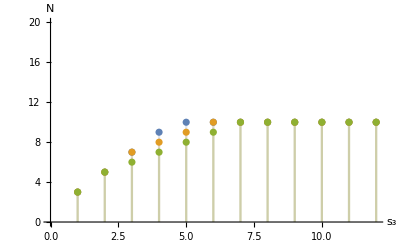

```mathematica
DiscretePlot[ { n[{9/2, 11/2, s3}, 1], n[{9/2, 11/2, s3}, 3], n[{9/2, 11/2, s3}, 5] }, {s3, 1, 12}, PlotRange -> {0, 20}, AxesLabel -> {"s_3", "N"} ]
```

#### 2.2 - Constraint analysis

Each section below may be evaluated individually, however, they must be evaluated sequentially, i.e., first impose conservation on x_1, then on x_2, then on x_3. Once conservation is imposed one can then check the point switch identities (if applicable). However, if the fields are not conserved, one can skip directly to imposing point switch identities.

##### 2.2.1 - Correlation function solutions

Solution generator

```mathematica
(* Evaluate first *)
Clear[coeffrules, coeffscomplex, coeffs, indepcoeffs, constraints, realityrules,
D1rules, D2rules, D3rules,
diff12rules, diff13rules,
solutions, Hlist, HlistI, H, X]

realityrules = {};
D1rules = {};
D2rules = {};
D3rules = {};
diff12rules = {};
diff13rules = {};
reality12rules = {};

constraints := coeffscomplex/.realityrules/.D1rules/.D2rules/.D3rules/.diff12rules/.diff13rules/.reality12rules//Expand;
coeffrules := MapThread[ Rule, {coeffscomplex, constraints} ];
indepcoeffs := Intersection[ coeffscomplex, constraints ];

sol := Solve[ 
K[[3]]+ K[[2]] + M[[1]] + L[[3]]+ L̄[[2]] == Is[[1]]&&
K̄[[3]]+ K̄[[2]] + M[[1]] + L̄[[3]]+ L[[2]] == Js[[1]]&&
K[[1]]+ K[[3]] + M[[2]] + L[[1]]+ L̄[[3]] == Is[[2]]&&
K̄[[1]]+ K̄[[3]] + M[[2]] + L̄[[1]]+ L[[3]] == Js[[2]]&&
K[[2]]+ K[[1]] + M[[3]] + L[[2]]+ L̄[[1]] == Is[[3]]&&
K̄[[2]]+ K̄[[1]] + M[[3]] + L̄[[2]]+ L[[1]] == Js[[3]], vars, NonNegativeIntegers];

solHS := Solve[ 
K[[3]]+ K[[2]] + L[[3]]+ L̄[[2]] == Is[[1]]&&
K̄[[3]]+ K̄[[2]] + L̄[[3]]+ L[[2]] == Js[[1]]&&
K[[1]]+ K[[3]] + L[[1]]+ L̄[[3]] == Is[[2]]&&
K̄[[1]]+ K̄[[3]] + L̄[[1]]+ L[[3]] == Js[[2]]&&
K[[2]]+ K[[1]] + L[[2]]+ L̄[[1]] == Is[[3]]&&
K̄[[2]]+ K̄[[1]] + L̄[[2]]+ L[[1]] == Js[[3]], Drop[vars, -3], NonNegativeIntegers];

(* Non-optimised   *)
solutions = sol; 
Hlist = If[ Spins == {0,0,0}, {A}, If[ solutions == {}, {}, F[P,Q,Z]/.solutions ] ]//Sort;

(* Higher-spin optimisations
solutions = If[ HS == { True, True, True }, solHS, sol ];
Hlist = If[ Spins == {0,0,0}, {A}, If[ solutions == {}, {}, F[P,Q,Z]/.solutions/.If[ HS == { True, True, True }, {M[[1]] -> 0, M[[2]] -> 0, M[[3]] -> 0 }, {}] ] ]//Sort;  *)

HlistI = SieveList[dep2][ Hlist ];
coeffs = Table[ Subscript[A,i], {i,1,Length[HlistI]} ];

(* Rules for conjugating solutions *)
conjugatecoeffs = MapThread[ Rule, {coeffs, Conjugate[coeffs] } ];
coeffsub = { Subscript[ A, i_] -> Subscript[ a, i] + I Subscript[ b, i] };
conjugatecoeffsub = { Conjugate[ Subscript[ A, i_] ] -> Subscript[ a, i] - I Subscript[ b, i] };
coeffscomplex = Join[ Table[ Subscript[a, i], {i, 1, Length[coeffs]} ], Table[ Subscript[b, i], {i, 1, Length[coeffs]} ] ];

(* Construction of ansatz *)
H = Sum[ coeffs[[i]]HlistI[[i]], {i,1,Length[coeffs]} ];

(* Expand the complex coefficients *)
Hcomplex = H/.coeffsub;
Hbcomplex = H/.conjugatecoeffs/.conjugatecoeffsub/.conjugatesol;

(* Presentation of solution *)
Hc := If[ q123 > 0, 
Collect[ X^q123 Hcomplex/.coeffrules, Join[ indepcoeffs, {X} ], Expand ],
Collect[ Hcomplex/.coeffrules, indepcoeffs, Expand ]/.MapThread[ Rule, {coeffscomplex, HoldForm/@ Evaluate[ X^q123 coeffscomplex] } ] ]

(* Default:
Hc := X^q123 Collect[ H/.Arules, indepA, Expand ];

For presentation:
Hc := X^q123 Collect[ H/.Arules, indepA, FullSimplify ];

Hc := If[ q123 > 0, 
Collect[ X^q123 H/.Arules, Join[ indepA, {X} ], Expand ],
Collect[ H/.Arules, indepA, Expand ]/.MapThread[ Rule, {coeffs, HoldForm/@ Evaluate[ X^q123 coeffs ] } ] ];*)
```

```mathematica
Hlist
HlistI
```

{Q_1^2 Q_2^2 Q_3^2,Q_1 Q_2 Q_3 Z_1 Z_2 Z_3,Z_1^2 Z_2^2 Z_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_1 Q_1 Q_2 Q_3 Z_1 (P̄)_1,P_2 Q_1 Q_2 Z_1 Z_2 (P̄)_1,P_3 Q_2 Z_1 Z_2 Z_3 (P̄)_1,P_1 Z_1^2 Z_2 Z_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 P_3 Q_2 Z_1 (P̄)_1^2,P_1^2 Z_1^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_2 Q_1 Q_2 Q_3 Z_2 (P̄)_2,P_3 Q_2 Q_3 Z_2 Z_3 (P̄)_2,P_1 Q_3 Z_1 Z_2 Z_3 (P̄)_2,P_2 Z_1 Z_2^2 Z_3 (P̄)_2,P_1 P_3 Q_2 Q_3 (P̄)_1 (P̄)_2,P_1^2 Q_3 Z_1 (P̄)_1 (P̄)_2,P_2 P_3 Q_2 Z_2 (P̄)_1 (P̄)_2,P_1 P_2 Z_1 Z_2 (P̄)_1 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_1 P_2 Q_3 Z_2 (P̄)_2^2,P_2^2 Z_2^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_3 Q_1 Q_2 Q_3 Z_3 (P̄)_3,P_1 Q_1 Q_3 Z_1 Z_3 (P̄)_3,P_2 Q_1 Z_1 Z_2 Z_3 (P̄)_3,P_3 Z_1 Z_2 Z_3^2 (P̄)_3,P_2 P_3 Q_1 Q_2 (P̄)_1 (P̄)_3,P_1 P_2 Q_1 Z_1 (P̄)_1 (P̄)_3,P_3^2 Q_2 Z_3 (P̄)_1 (P̄)_3,P_1 P_3 Z_1 Z_3 (P̄)_1 (P̄)_3,P_1 P_2 Q_1 Q_3 (P̄)_2 (P̄)_3,P_2^2 Q_1 Z_2 (P̄)_2 (P̄)_3,P_1 P_3 Q_3 Z_3 (P̄)_2 (P̄)_3,P_2 P_3 Z_2 Z_3 (P̄)_2 (P̄)_3,P_1 P_2 P_3 (P̄)_1 (P̄)_2 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_2 P_3 Q_1 Z_3 (P̄)_3^2,P_3^2 Z_3^2 (P̄)_3^2,Q_1^2 Q_2 Q_3 Z_1 (Q̄)_1,Q_1 Z_1^2 Z_2 Z_3 (Q̄)_1,P_3 Q_1 Q_2 Z_1 (P̄)_1 (Q̄)_1,P_1 Q_1 Z_1^2 (P̄)_1 (Q̄)_1,P_3 Q_1 Q_2 Q_3 (P̄)_2 (Q̄)_1,P_1 Q_1 Q_3 Z_1 (P̄)_2 (Q̄)_1,P_2 Q_1 Z_1 Z_2 (P̄)_2 (Q̄)_1,P_3 Z_1 Z_2 Z_3 (P̄)_2 (Q̄)_1,P_3^2 Q_2 (P̄)_1 (P̄)_2 (Q̄)_1,P_1 P_3 Z_1 (P̄)_1 (P̄)_2 (Q̄)_1,P_1 P_3 Q_3 (P̄)_2^2 (Q̄)_1,P_2 P_3 Z_2 (P̄)_2^2 (Q̄)_1,P_2 Q_1^2 Z_1 (P̄)_3 (Q̄)_1,P_3 Q_1 Z_1 Z_3 (P̄)_3 (Q̄)_1,P_2 P_3 Q_1 (P̄)_2 (P̄)_3 (Q̄)_1,P_3^2 Z_3 (P̄)_2 (P̄)_3 (Q̄)_1,Q_1^2 Z_1^2 (Q̄)_1^2,P_3 Q_1 Z_1 (P̄)_2 (Q̄)_1^2,P_3^2 (P̄)_2^2 (Q̄)_1^2,Q_1 Q_2^2 Q_3 Z_2 (Q̄)_2,Q_2 Z_1 Z_2^2 Z_3 (Q̄)_2,P_3 Q_2^2 Z_2 (P̄)_1 (Q̄)_2,P_1 Q_2 Z_1 Z_2 (P̄)_1 (Q̄)_2,P_1 Q_2 Q_3 Z_2 (P̄)_2 (Q̄)_2,P_2 Q_2 Z_2^2 (P̄)_2 (Q̄)_2,P_1 Q_1 Q_2 Q_3 (P̄)_3 (Q̄)_2,P_2 Q_1 Q_2 Z_2 (P̄)_3 (Q̄)_2,P_3 Q_2 Z_2 Z_3 (P̄)_3 (Q̄)_2,P_1 Z_1 Z_2 Z_3 (P̄)_3 (Q̄)_2,P_1 P_3 Q_2 (P̄)_1 (P̄)_3 (Q̄)_2,P_1^2 Z_1 (P̄)_1 (P̄)_3 (Q̄)_2,P_1^2 Q_3 (P̄)_2 (P̄)_3 (Q̄)_2,P_1 P_2 Z_2 (P̄)_2 (P̄)_3 (Q̄)_2,P_1 P_2 Q_1 (P̄)_3^2 (Q̄)_2,P_1 P_3 Z_3 (P̄)_3^2 (Q̄)_2,Q_1 Q_2 Z_1 Z_2 (Q̄)_1 (Q̄)_2,P_3 Q_2 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2,P_1 Z_1 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 Q_1 Z_1 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 P_3 (P̄)_2 (P̄)_3 (Q̄)_1 (Q̄)_2,Q_2^2 Z_2^2 (Q̄)_2^2,P_1 Q_2 Z_2 (P̄)_3 (Q̄)_2^2,P_1^2 (P̄)_3^2 (Q̄)_2^2,Q_1 Q_2 Q_3^2 Z_3 (Q̄)_3,Q_3 Z_1 Z_2 Z_3^2 (Q̄)_3,P_2 Q_1 Q_2 Q_3 (P̄)_1 (Q̄)_3,P_3 Q_2 Q_3 Z_3 (P̄)_1 (Q̄)_3,P_1 Q_3 Z_1 Z_3 (P̄)_1 (Q̄)_3,P_2 Z_1 Z_2 Z_3 (P̄)_1 (Q̄)_3,P_2 P_3 Q_2 (P̄)_1^2 (Q̄)_3,P_1 P_2 Z_1 (P̄)_1^2 (Q̄)_3,P_1 Q_3^2 Z_3 (P̄)_2 (Q̄)_3,P_2 Q_3 Z_2 Z_3 (P̄)_2 (Q̄)_3,P_1 P_2 Q_3 (P̄)_1 (P̄)_2 (Q̄)_3,P_2^2 Z_2 (P̄)_1 (P̄)_2 (Q̄)_3,P_2 Q_1 Q_3 Z_3 (P̄)_3 (Q̄)_3,P_3 Q_3 Z_3^2 (P̄)_3 (Q̄)_3,P_2^2 Q_1 (P̄)_1 (P̄)_3 (Q̄)_3,P_2 P_3 Z_3 (P̄)_1 (P̄)_3 (Q̄)_3,Q_1 Q_3 Z_1 Z_3 (Q̄)_1 (Q̄)_3,P_2 Q_1 Z_1 (P̄)_1 (Q̄)_1 (Q̄)_3,P_3 Z_1 Z_3 (P̄)_1 (Q̄)_1 (Q̄)_3,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_3 Q_3 Z_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_2 P_3 (P̄)_1 (P̄)_2 (Q̄)_1 (Q̄)_3,Q_2 Q_3 Z_2 Z_3 (Q̄)_2 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_2 Z_2 (P̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 Z_3 (P̄)_3 (Q̄)_2 (Q̄)_3,P_2 Z_2 Z_3 (P̄)_3 (Q̄)_2 (Q̄)_3,P_1 P_2 (P̄)_1 (P̄)_3 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,Z_1 Z_2 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Z_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Z_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Z_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,P_3 (P̄)_2 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,Q_2 Z_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,P_1 (P̄)_3 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,Q_3^2 Z_3^2 (Q̄)_3^2,P_2 Q_3 Z_3 (P̄)_1 (Q̄)_3^2,P_2^2 (P̄)_1^2 (Q̄)_3^2,Q_3 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,P_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

{Q_1^2 Q_2^2 Q_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

```mathematica
Hlist/.blocksub;
HlistI/.blocksub;
```

Independent solutions

The sieve function is applied to construct a linearly independent basis of solutions. This will eliminate all Z’s in place of P’s and Q’s where possible.

```mathematica
Hlist//Length
Hlist

HlistI//Length
HlistI
```

130

{Q_1^2 Q_2^2 Q_3^2,Q_1 Q_2 Q_3 Z_1 Z_2 Z_3,Z_1^2 Z_2^2 Z_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_1 Q_1 Q_2 Q_3 Z_1 (P̄)_1,P_2 Q_1 Q_2 Z_1 Z_2 (P̄)_1,P_3 Q_2 Z_1 Z_2 Z_3 (P̄)_1,P_1 Z_1^2 Z_2 Z_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 P_3 Q_2 Z_1 (P̄)_1^2,P_1^2 Z_1^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_2 Q_1 Q_2 Q_3 Z_2 (P̄)_2,P_3 Q_2 Q_3 Z_2 Z_3 (P̄)_2,P_1 Q_3 Z_1 Z_2 Z_3 (P̄)_2,P_2 Z_1 Z_2^2 Z_3 (P̄)_2,P_1 P_3 Q_2 Q_3 (P̄)_1 (P̄)_2,P_1^2 Q_3 Z_1 (P̄)_1 (P̄)_2,P_2 P_3 Q_2 Z_2 (P̄)_1 (P̄)_2,P_1 P_2 Z_1 Z_2 (P̄)_1 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_1 P_2 Q_3 Z_2 (P̄)_2^2,P_2^2 Z_2^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_3 Q_1 Q_2 Q_3 Z_3 (P̄)_3,P_1 Q_1 Q_3 Z_1 Z_3 (P̄)_3,P_2 Q_1 Z_1 Z_2 Z_3 (P̄)_3,P_3 Z_1 Z_2 Z_3^2 (P̄)_3,P_2 P_3 Q_1 Q_2 (P̄)_1 (P̄)_3,P_1 P_2 Q_1 Z_1 (P̄)_1 (P̄)_3,P_3^2 Q_2 Z_3 (P̄)_1 (P̄)_3,P_1 P_3 Z_1 Z_3 (P̄)_1 (P̄)_3,P_1 P_2 Q_1 Q_3 (P̄)_2 (P̄)_3,P_2^2 Q_1 Z_2 (P̄)_2 (P̄)_3,P_1 P_3 Q_3 Z_3 (P̄)_2 (P̄)_3,P_2 P_3 Z_2 Z_3 (P̄)_2 (P̄)_3,P_1 P_2 P_3 (P̄)_1 (P̄)_2 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_2 P_3 Q_1 Z_3 (P̄)_3^2,P_3^2 Z_3^2 (P̄)_3^2,Q_1^2 Q_2 Q_3 Z_1 (Q̄)_1,Q_1 Z_1^2 Z_2 Z_3 (Q̄)_1,P_3 Q_1 Q_2 Z_1 (P̄)_1 (Q̄)_1,P_1 Q_1 Z_1^2 (P̄)_1 (Q̄)_1,P_3 Q_1 Q_2 Q_3 (P̄)_2 (Q̄)_1,P_1 Q_1 Q_3 Z_1 (P̄)_2 (Q̄)_1,P_2 Q_1 Z_1 Z_2 (P̄)_2 (Q̄)_1,P_3 Z_1 Z_2 Z_3 (P̄)_2 (Q̄)_1,P_3^2 Q_2 (P̄)_1 (P̄)_2 (Q̄)_1,P_1 P_3 Z_1 (P̄)_1 (P̄)_2 (Q̄)_1,P_1 P_3 Q_3 (P̄)_2^2 (Q̄)_1,P_2 P_3 Z_2 (P̄)_2^2 (Q̄)_1,P_2 Q_1^2 Z_1 (P̄)_3 (Q̄)_1,P_3 Q_1 Z_1 Z_3 (P̄)_3 (Q̄)_1,P_2 P_3 Q_1 (P̄)_2 (P̄)_3 (Q̄)_1,P_3^2 Z_3 (P̄)_2 (P̄)_3 (Q̄)_1,Q_1^2 Z_1^2 (Q̄)_1^2,P_3 Q_1 Z_1 (P̄)_2 (Q̄)_1^2,P_3^2 (P̄)_2^2 (Q̄)_1^2,Q_1 Q_2^2 Q_3 Z_2 (Q̄)_2,Q_2 Z_1 Z_2^2 Z_3 (Q̄)_2,P_3 Q_2^2 Z_2 (P̄)_1 (Q̄)_2,P_1 Q_2 Z_1 Z_2 (P̄)_1 (Q̄)_2,P_1 Q_2 Q_3 Z_2 (P̄)_2 (Q̄)_2,P_2 Q_2 Z_2^2 (P̄)_2 (Q̄)_2,P_1 Q_1 Q_2 Q_3 (P̄)_3 (Q̄)_2,P_2 Q_1 Q_2 Z_2 (P̄)_3 (Q̄)_2,P_3 Q_2 Z_2 Z_3 (P̄)_3 (Q̄)_2,P_1 Z_1 Z_2 Z_3 (P̄)_3 (Q̄)_2,P_1 P_3 Q_2 (P̄)_1 (P̄)_3 (Q̄)_2,P_1^2 Z_1 (P̄)_1 (P̄)_3 (Q̄)_2,P_1^2 Q_3 (P̄)_2 (P̄)_3 (Q̄)_2,P_1 P_2 Z_2 (P̄)_2 (P̄)_3 (Q̄)_2,P_1 P_2 Q_1 (P̄)_3^2 (Q̄)_2,P_1 P_3 Z_3 (P̄)_3^2 (Q̄)_2,Q_1 Q_2 Z_1 Z_2 (Q̄)_1 (Q̄)_2,P_3 Q_2 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2,P_1 Z_1 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 Q_1 Z_1 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 P_3 (P̄)_2 (P̄)_3 (Q̄)_1 (Q̄)_2,Q_2^2 Z_2^2 (Q̄)_2^2,P_1 Q_2 Z_2 (P̄)_3 (Q̄)_2^2,P_1^2 (P̄)_3^2 (Q̄)_2^2,Q_1 Q_2 Q_3^2 Z_3 (Q̄)_3,Q_3 Z_1 Z_2 Z_3^2 (Q̄)_3,P_2 Q_1 Q_2 Q_3 (P̄)_1 (Q̄)_3,P_3 Q_2 Q_3 Z_3 (P̄)_1 (Q̄)_3,P_1 Q_3 Z_1 Z_3 (P̄)_1 (Q̄)_3,P_2 Z_1 Z_2 Z_3 (P̄)_1 (Q̄)_3,P_2 P_3 Q_2 (P̄)_1^2 (Q̄)_3,P_1 P_2 Z_1 (P̄)_1^2 (Q̄)_3,P_1 Q_3^2 Z_3 (P̄)_2 (Q̄)_3,P_2 Q_3 Z_2 Z_3 (P̄)_2 (Q̄)_3,P_1 P_2 Q_3 (P̄)_1 (P̄)_2 (Q̄)_3,P_2^2 Z_2 (P̄)_1 (P̄)_2 (Q̄)_3,P_2 Q_1 Q_3 Z_3 (P̄)_3 (Q̄)_3,P_3 Q_3 Z_3^2 (P̄)_3 (Q̄)_3,P_2^2 Q_1 (P̄)_1 (P̄)_3 (Q̄)_3,P_2 P_3 Z_3 (P̄)_1 (P̄)_3 (Q̄)_3,Q_1 Q_3 Z_1 Z_3 (Q̄)_1 (Q̄)_3,P_2 Q_1 Z_1 (P̄)_1 (Q̄)_1 (Q̄)_3,P_3 Z_1 Z_3 (P̄)_1 (Q̄)_1 (Q̄)_3,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_3 Q_3 Z_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_2 P_3 (P̄)_1 (P̄)_2 (Q̄)_1 (Q̄)_3,Q_2 Q_3 Z_2 Z_3 (Q̄)_2 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_2 Z_2 (P̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 Z_3 (P̄)_3 (Q̄)_2 (Q̄)_3,P_2 Z_2 Z_3 (P̄)_3 (Q̄)_2 (Q̄)_3,P_1 P_2 (P̄)_1 (P̄)_3 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,Z_1 Z_2 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Z_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Z_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Z_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,P_3 (P̄)_2 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,Q_2 Z_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,P_1 (P̄)_3 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,Q_3^2 Z_3^2 (Q̄)_3^2,P_2 Q_3 Z_3 (P̄)_1 (Q̄)_3^2,P_2^2 (P̄)_1^2 (Q̄)_3^2,Q_3 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,P_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

15

{Q_1^2 Q_2^2 Q_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

```mathematica
coeffs
coeffscomplex
```

{A_1,A_2,A_3,A_4,A_5,A_6,A_7,A_8,A_9,A_10,A_11,A_12,A_13,A_14,A_15}

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,a_11,a_12,a_13,a_14,a_15,b_1,b_2,b_3,b_4,b_5,b_6,b_7,b_8,b_9,b_10,b_11,b_12,b_13,b_14,b_15}

```mathematica
Hc
```

a_1/X^4 Q_1^2 Q_2^2 Q_3^2+ⅈ b_1/X^4 Q_1^2 Q_2^2 Q_3^2+a_2/X^4 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+ⅈ b_2/X^4 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+a_3/X^4 P_3^2 Q_2^2 (P̄)_1^2+ⅈ b_3/X^4 P_3^2 Q_2^2 (P̄)_1^2+a_4/X^4 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+ⅈ b_4/X^4 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+a_5/X^4 P_1^2 Q_3^2 (P̄)_2^2+ⅈ b_5/X^4 P_1^2 Q_3^2 (P̄)_2^2+a_6/X^4 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+ⅈ b_6/X^4 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+a_7/X^4 P_2^2 Q_1^2 (P̄)_3^2+ⅈ b_7/X^4 P_2^2 Q_1^2 (P̄)_3^2+a_8/X^4 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+ⅈ b_8/X^4 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+a_9/X^4 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+ⅈ b_9/X^4 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+a_10/X^4 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_10/X^4 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+a_11/X^4 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_11/X^4 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_12/X^4 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_12/X^4 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_13/X^4 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_13/X^4 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_14/X^4 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_14/X^4 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_15/X^4 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2+ⅈ b_15/X^4 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

Reset constraints

```mathematica
(* Evaluate first *)
Clear[realityrules, realityeqns, realitysimp,
D1rules, D2rules, D3rules,
D1List, D1ListI, D1eqns, D1,
D2List, D2ListI, D2eqns, D2,
D3List, D3ListI, D3eqns, D3,
diff12rules, diff13rules,
reality12rules, reality12eqns, reality12simp]

realityrules = {};
D1rules = {};
D2rules = {};
D3rules = {};
diff12rules = {};
diff13rules = {};
reality12rules = {};

constraints
coeffrules
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,a_11,a_12,a_13,a_14,a_15,b_1,b_2,b_3,b_4,b_5,b_6,b_7,b_8,b_9,b_10,b_11,b_12,b_13,b_14,b_15}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→a_4,a_5→a_5,a_6→a_6,a_7→a_7,a_8→a_8,a_9→a_9,a_10→a_10,a_11→a_11,a_12→a_12,a_13→a_13,a_14→a_14,a_15→a_15,b_1→b_1,b_2→b_2,b_3→b_3,b_4→b_4,b_5→b_5,b_6→b_6,b_7→b_7,b_8→b_8,b_9→b_9,b_10→b_10,b_11→b_11,b_12→b_12,b_13→b_13,b_14→b_14,b_15→b_15}

##### 2.2.2 - Parity and reality conditions (bosonic currents)

Parity-even and parity-odd solutions

Check the inversion properties of each structure:

```mathematica
(* H^I(X) *)
SieveExpr[dep2][ H/.invertstructures ];
Hinverted = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ]

(* H^c(X) *)
SieveExpr[dep2][ H/.conjugatesol ];
Hsemibar = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ]
```

(A_3+A_5+A_7+A_12+A_13+A_14+A_15) Q_1^2 Q_2^2 Q_3^2+(2 A_3+A_12) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+A_3 P_3^2 Q_2^2 (P̄)_1^2+(2 A_5+A_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+A_5 P_1^2 Q_3^2 (P̄)_2^2+(2 A_7+A_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+A_7 P_2^2 Q_1^2 (P̄)_3^2+A_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+A_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+A_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3+A_4-2 A_5+A_6-2 A_7+A_11-A_12-A_13-A_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_4-2 A_5) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_6-2 A_7) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_1-A_2+A_3-A_4+A_5-A_6+A_7) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

(A_3+A_5+A_7+A_12+A_13+A_14+A_15) Q_1^2 Q_2^2 Q_3^2+(2 A_3+A_12) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+A_3 P_3^2 Q_2^2 (P̄)_1^2+(2 A_5+A_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+A_5 P_1^2 Q_3^2 (P̄)_2^2+(2 A_7+A_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+A_7 P_2^2 Q_1^2 (P̄)_3^2+A_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+A_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+A_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3+A_4-2 A_5+A_6-2 A_7+A_11-A_12-A_13-A_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_4-2 A_5) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_6-2 A_7) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_1-A_2+A_3-A_4+A_5-A_6+A_7) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

```mathematica
(* Construct parity-even solutions *)
SieveExpr[dep2][ Hinverted - (-1)^(Spins//Total) H ];
Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ]

MonomialList[ %, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
MapThread[Equal, {%, ConstantArray[0,Length[%]]}];
Solve[ %//Expand, coeffs]//Flatten

Collect[ H/.%, coeffs ]
HlistEI = DeleteCases[ Coefficient[%, #, 1]&/@coeffs, 0 ]

(* Construct parity-odd solutions *)
SieveExpr[dep2][ Hinverted + (-1)^(Spins//Total) H ];
Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ]

MonomialList[ %, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
MapThread[Equal, {%, ConstantArray[0,Length[%]]}];
Solve[ %//Expand, coeffs]//Flatten

Collect[ H/.%, coeffs ]
HlistOI = DeleteCases[ Coefficient[%, #, 1]&/@coeffs, 0 ]
```

(-A_1+A_3+A_5+A_7+A_12+A_13+A_14+A_15) Q_1^2 Q_2^2 Q_3^2+(-A_2+2 A_3+A_12) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+(-A_4+2 A_5+A_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+(-A_6+2 A_7+A_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+(A_2-2 A_3+A_4-2 A_5+A_6-2 A_7-A_12-A_13-A_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3-A_12) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_4-2 A_5-A_13) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_6-2 A_7-A_14) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_1-A_2+A_3-A_4+A_5-A_6+A_7-A_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

Solve::svars: Equations may not give solutions for all "solve" variables.

{A_12→A_2-2 A_3,A_13→A_4-2 A_5,A_14→A_6-2 A_7,A_15→A_1-A_2+A_3-A_4+A_5-A_6+A_7}

A_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+A_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+A_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+A_11 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+A_2 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_4 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_6 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_1 (Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_3 (P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_5 (P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_7 (P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

{Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3}

(A_1+A_3+A_5+A_7+A_12+A_13+A_14+A_15) Q_1^2 Q_2^2 Q_3^2+(A_2+2 A_3+A_12) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+2 A_3 P_3^2 Q_2^2 (P̄)_1^2+(A_4+2 A_5+A_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 A_5 P_1^2 Q_3^2 (P̄)_2^2+(A_6+2 A_7+A_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 A_7 P_2^2 Q_1^2 (P̄)_3^2+2 A_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+2 A_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 A_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3+A_4-2 A_5+A_6-2 A_7+2 A_11-A_12-A_13-A_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_2-2 A_3+A_12) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_4-2 A_5+A_13) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_6-2 A_7+A_14) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(A_1-A_2+A_3-A_4+A_5-A_6+A_7+A_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

Solve::svars: Equations may not give solutions for all "solve" variables.

{A_3→0,A_5→0,A_7→0,A_8→0,A_9→0,A_10→0,A_11→-A_2-A_4-A_6,A_12→-A_2,A_13→-A_4,A_14→-A_6,A_15→-A_1+A_2+A_4+A_6}

A_1 (Q_1^2 Q_2^2 Q_3^2-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_2 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_4 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_6 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

{Q_1^2 Q_2^2 Q_3^2-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

Test that the structures possess the appropriate transformation properties:

```mathematica
HlistEI
SieveExpr[dep2][ %/.invertstructures ]
% - (-1)^(Spins//Total) %%

HlistOI
SieveExpr[dep2][ %/.invertstructures ]
% + (-1)^(Spins//Total) %%
```

{Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3}

{Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3}

{0,0,0,0,0,0,0,0,0,0,0}

{Q_1^2 Q_2^2 Q_3^2-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

{-Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,-P_3 Q_1 Q_2^2 Q_3 (P̄)_1+Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,-P_1 Q_1 Q_2 Q_3^2 (P̄)_2+Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,-P_2 Q_1^2 Q_2 Q_3 (P̄)_3+Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

{0,0,0,0}

```mathematica
Hparity = Sum[ Subscript[A, i]HlistEI[[i]], {i,1, Length[HlistEI]}] + Sum[ Subscript[B, i]HlistOI[[i]], {i,1, Length[HlistOI]}]
```

A_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+A_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+A_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+A_11 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+B_1 (Q_1^2 Q_2^2 Q_3^2-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_2 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_4 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_6 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_1 (Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_3 (P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+B_2 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_5 (P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+B_3 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+A_7 (P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+B_4 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3-Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

Hence, we see that the a’s correspond to parity-even solutions, while the b’s correspond to parity-odd solutions.

Reality condition

```mathematica
SieveExpr[dep2][ Hcomplex - Hbcomplex ];
realitysimp = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ] 

MonomialList[ realitysimp, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
realityeqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
realityrules = Solve[ realityeqns//Expand, coeffscomplex ]//Flatten
```

(a_1-a_3-a_5-a_7-a_12-a_13-a_14-a_15+ⅈ b_1+ⅈ b_3+ⅈ b_5+ⅈ b_7+ⅈ b_12+ⅈ b_13+ⅈ b_14+ⅈ b_15) Q_1^2 Q_2^2 Q_3^2+(a_2-2 a_3-a_12+ⅈ b_2+2 ⅈ b_3+ⅈ b_12) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+2 ⅈ b_3 P_3^2 Q_2^2 (P̄)_1^2+(a_4-2 a_5-a_13+ⅈ b_4+2 ⅈ b_5+ⅈ b_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 ⅈ b_5 P_1^2 Q_3^2 (P̄)_2^2+(a_6-2 a_7-a_14+ⅈ b_6+2 ⅈ b_7+ⅈ b_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 ⅈ b_7 P_2^2 Q_1^2 (P̄)_3^2+2 ⅈ b_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+2 ⅈ b_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 ⅈ b_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(-a_2+2 a_3-a_4+2 a_5-a_6+2 a_7+a_12+a_13+a_14+ⅈ b_2-2 ⅈ b_3+ⅈ b_4-2 ⅈ b_5+ⅈ b_6-2 ⅈ b_7+2 ⅈ b_11-ⅈ b_12-ⅈ b_13-ⅈ b_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_2+2 a_3+a_12+ⅈ b_2-2 ⅈ b_3+ⅈ b_12) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_4+2 a_5+a_13+ⅈ b_4-2 ⅈ b_5+ⅈ b_13) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_6+2 a_7+a_14+ⅈ b_6-2 ⅈ b_7+ⅈ b_14) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_1+a_2-a_3+a_4-a_5+a_6-a_7+a_15+ⅈ b_1-ⅈ b_2+ⅈ b_3-ⅈ b_4+ⅈ b_5-ⅈ b_6+ⅈ b_7+ⅈ b_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

{True,2 b_5==0,True,2 b_10==0,a_4-2 a_5-a_13==0,b_4+2 b_5+b_13==0,-a_4+2 a_5+a_13==0,b_4-2 b_5+b_13==0,True,2 b_7==0,True,2 b_9==0,a_6-2 a_7-a_14==0,b_6+2 b_7+b_14==0,-a_6+2 a_7+a_14==0,b_6-2 b_7+b_14==0,True,2 b_3==0,a_2-2 a_3-a_12==0,b_2+2 b_3+b_12==0,-a_2+2 a_3+a_12==0,b_2-2 b_3+b_12==0,True,2 b_8==0,a_1-a_3-a_5-a_7-a_12-a_13-a_14-a_15==0,b_1+b_3+b_5+b_7+b_12+b_13+b_14+b_15==0,-a_2+2 a_3-a_4+2 a_5-a_6+2 a_7+a_12+a_13+a_14==0,b_2-2 b_3+b_4-2 b_5+b_6-2 b_7+2 b_11-b_12-b_13-b_14==0,-a_1+a_2-a_3+a_4-a_5+a_6-a_7+a_15==0,b_1-b_2+b_3-b_4+b_5-b_6+b_7+b_15==0}

Solve::svars: Equations may not give solutions for all "solve" variables.

{a_12→a_2-2 a_3,a_13→a_4-2 a_5,a_14→a_6-2 a_7,a_15→a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_3→0,b_5→0,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-b_2-b_4-b_6,b_12→-b_2,b_13→-b_4,b_14→-b_6,b_15→-b_1+b_2+b_4+b_6}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,a_11,a_2-2 a_3,a_4-2 a_5,a_6-2 a_7,a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_1,b_2,0,b_4,0,b_6,0,0,0,0,-b_2-b_4-b_6,-b_2,-b_4,-b_6,-b_1+b_2+b_4+b_6}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→a_4,a_5→a_5,a_6→a_6,a_7→a_7,a_8→a_8,a_9→a_9,a_10→a_10,a_11→a_11,a_12→a_2-2 a_3,a_13→a_4-2 a_5,a_14→a_6-2 a_7,a_15→a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_1→b_1,b_2→b_2,b_3→0,b_4→b_4,b_5→0,b_6→b_6,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-b_2-b_4-b_6,b_12→-b_2,b_13→-b_4,b_14→-b_6,b_15→-b_1+b_2+b_4+b_6}

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs
coeffrules
Hc
```

15

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,a_11,b_1,b_2,b_4,b_6}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→a_4,a_5→a_5,a_6→a_6,a_7→a_7,a_8→a_8,a_9→a_9,a_10→a_10,a_11→a_11,a_12→a_2-2 a_3,a_13→a_4-2 a_5,a_14→a_6-2 a_7,a_15→a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_1→b_1,b_2→b_2,b_3→0,b_4→b_4,b_5→0,b_6→b_6,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-b_2-b_4-b_6,b_12→-b_2,b_13→-b_4,b_14→-b_6,b_15→-b_1+b_2+b_4+b_6}

a_8/X^4 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+a_9/X^4 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+a_10/X^4 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+a_11/X^4 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_4/X^4 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_6/X^4 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_1/X^4 (ⅈ Q_1^2 Q_2^2 Q_3^2-ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_2/X^4 (ⅈ P_3 Q_1 Q_2^2 Q_3 (P̄)_1-ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_4/X^4 (ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2-ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_6/X^4 (ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3-ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_5/X^4 (P_1^2 Q_3^2 (P̄)_2^2-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_7/X^4 (P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

##### 2.2.3 - Conservation I

Conservation at x_1

Compute conservation on each of the structures in our linearly independent list:

```mathematica
D1List = ( D1F/.indexvals[HlistI]//Expand )/.{δ -> q123, X -> 1}//Together
D1ListI = SieveExpr[dep2][ D1List ]
```

{-8 (2 Q_1 Q_2 Q_3 Z_2 Z_3+Q_1^2 Q_2 Q_3 (Q̄)_1),-4 (P_1 Q_1 Q_2 Q_3 (P̄)_1+P_3 Q_2 Z_2 Z_3 (P̄)_1+2 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1),0,-4 (P_1 Q_1 Q_2 Q_3 (P̄)_1+P_1 Q_3 Z_2 Z_3 (P̄)_2+2 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1),0,-4 (P_1 Q_1 Q_2 Q_3 (P̄)_1-P_2 Q_1 Q_2 Z_2 (P̄)_1-P_1 Q_1 Q_3 Z_3 (P̄)_3+P_2 Q_1 Z_2 Z_3 (P̄)_3-2 Q_1^2 Q_2 Q_3 (Q̄)_1+P_2 Q_1^2 (P̄)_3 (Q̄)_1),-8 (2 P_1 P_2 Q_1 (P̄)_1 (P̄)_3-3 P_2 Q_1^2 (P̄)_3 (Q̄)_1),-8 (P_3 Q_1 Z_3 (P̄)_3 (Q̄)_1+Q_1 Q_2 Z_2 (Q̄)_1 (Q̄)_2),-8 (P_2 Q_1 Z_2 (P̄)_2 (Q̄)_1+Q_1 Q_3 Z_3 (Q̄)_1 (Q̄)_3),-4 (P_1 Q_1 Q_2 Q_3 (P̄)_1+P_1 Q_2 Z_2 (P̄)_1 (Q̄)_2+P_1 Q_3 Z_3 (P̄)_1 (Q̄)_3+P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3),-2 (Q_1 Q_2 Q_3 Z_2 Z_3+2 Q_1^2 Q_2 Q_3 (Q̄)_1+3 Q_1 Q_2 Z_2 (Q̄)_1 (Q̄)_2+3 Q_1 Q_3 Z_3 (Q̄)_1 (Q̄)_3+Z_2 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3),-2 (P_3 Q_2 Z_2 Z_3 (P̄)_1+2 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-P_1 Q_2 Z_2 (P̄)_1 (Q̄)_2+3 P_3 Z_3 (P̄)_1 (Q̄)_1 (Q̄)_3),-2 (P_1 Q_3 Z_2 Z_3 (P̄)_2+2 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1+3 P_1 Z_2 (P̄)_2 (Q̄)_1 (Q̄)_2-P_1 Q_3 Z_3 (P̄)_1 (Q̄)_3),-2 (P_2 Q_1 Z_2 Z_3 (P̄)_3+3 P_2 Q_1^2 (P̄)_3 (Q̄)_1+P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3),-8 (2 Z_2 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3)}

{16 P_1 Q_1 Q_2 Q_3 (P̄)_1-24 Q_1^2 Q_2 Q_3 (Q̄)_1,-4 P_1 Q_1 Q_2 Q_3 (P̄)_1+4 P_1 P_3 Q_2 (P̄)_1^2-12 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1,0,-4 P_1 Q_1 Q_2 Q_3 (P̄)_1+4 P_1^2 Q_3 (P̄)_1 (P̄)_2-12 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1,0,-16 P_1 Q_1 Q_2 Q_3 (P̄)_1+4 Q_1^2 Q_2 Q_3 (Q̄)_1-8 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-8 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1-8 P_2 Q_1^2 (P̄)_3 (Q̄)_1+4 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,16 P_1 Q_1 Q_2 Q_3 (P̄)_1+16 Q_1^2 Q_2 Q_3 (Q̄)_1+16 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1+16 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1+24 P_2 Q_1^2 (P̄)_3 (Q̄)_1-16 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,8 P_2 Q_1^2 (P̄)_3 (Q̄)_1-8 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,8 P_2 Q_1^2 (P̄)_3 (Q̄)_1-8 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,-12 P_1 Q_1 Q_2 Q_3 (P̄)_1-4 P_1 P_3 Q_2 (P̄)_1^2-4 P_1^2 Q_3 (P̄)_1 (P̄)_2-4 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,2 P_1 Q_1 Q_2 Q_3 (P̄)_1-18 Q_1^2 Q_2 Q_3 (Q̄)_1-6 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-6 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1+2 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,2 P_1 Q_1 Q_2 Q_3 (P̄)_1+4 P_1 P_3 Q_2 (P̄)_1^2+6 Q_1^2 Q_2 Q_3 (Q̄)_1-6 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1+6 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1+6 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,2 P_1 Q_1 Q_2 Q_3 (P̄)_1+4 P_1^2 Q_3 (P̄)_1 (P̄)_2+6 Q_1^2 Q_2 Q_3 (Q̄)_1+6 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-6 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1+6 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,-2 P_1 Q_1 Q_2 Q_3 (P̄)_1-2 Q_1^2 Q_2 Q_3 (Q̄)_1-2 P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-2 P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1-8 P_2 Q_1^2 (P̄)_3 (Q̄)_1-2 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+10 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3,16 P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-24 Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3}

The derivative is:

```mathematica
Sum[ coeffs[[i]] D1ListI[[i]], {i, 1, Length[coeffs]} ];
D1 = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants  ]/.coeffsub
```

2 (a_11+a_12+a_13-a_14+8 (a_1+ⅈ b_1)-2 (a_2+ⅈ b_2)-2 (a_4+ⅈ b_4)-8 (a_6+ⅈ b_6)+8 (a_7+ⅈ b_7)-6 (a_10+ⅈ b_10)+ⅈ b_11+ⅈ b_12+ⅈ b_13-ⅈ b_14) P_1 Q_1 Q_2 Q_3 (P̄)_1+4 (a_2-a_10+a_12+ⅈ b_2-ⅈ b_10+ⅈ b_12) P_1 P_3 Q_2 (P̄)_1^2+4 (a_4-a_10+a_13+ⅈ b_4-ⅈ b_10+ⅈ b_13) P_1^2 Q_3 (P̄)_1 (P̄)_2-2 (a_14+12 (a_1+ⅈ b_1)-2 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)+9 (a_11+ⅈ b_11)-3 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)+ⅈ b_14) Q_1^2 Q_2 Q_3 (Q̄)_1-2 (a_14+6 (a_2+ⅈ b_2)+4 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)+3 (a_11+ⅈ b_11)+3 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)+ⅈ b_14) P_3 Q_1 Q_2 (P̄)_1 (Q̄)_1-2 (a_14+6 (a_4+ⅈ b_4)+4 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)+3 (a_11+ⅈ b_11)-3 (a_12+ⅈ b_12)+3 (a_13+ⅈ b_13)+ⅈ b_14) P_1 Q_1 Q_3 (P̄)_2 (Q̄)_1-8 (a_6-a_8-a_9+a_14+ⅈ b_6-3 (a_7+ⅈ b_7)-ⅈ b_8-ⅈ b_9+ⅈ b_14) P_2 Q_1^2 (P̄)_3 (Q̄)_1+2 (a_11-a_14-2 (a_10+ⅈ b_10)+ⅈ b_11+3 (a_12+ⅈ b_12)+3 (a_13+ⅈ b_13)-ⅈ b_14+8 (a_15+ⅈ b_15)) P_1 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 (2 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)-4 (a_8+ⅈ b_8)-4 (a_9+ⅈ b_9)-3 (a_11+ⅈ b_11)-3 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)+5 (a_14+ⅈ b_14)-12 (a_15+ⅈ b_15)) Q_1 (Q̄)_1^2 (Q̄)_2 (Q̄)_3

Normalise the solution and reduce to 0.

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10,a_11,a_2-2 a_3,a_4-2 a_5,a_6-2 a_7,a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_1,b_2,0,b_4,0,b_6,0,0,0,0,-b_2-b_4-b_6,-b_2,-b_4,-b_6,-b_1+b_2+b_4+b_6}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→a_4,a_5→a_5,a_6→a_6,a_7→a_7,a_8→a_8,a_9→a_9,a_10→a_10,a_11→a_11,a_12→a_2-2 a_3,a_13→a_4-2 a_5,a_14→a_6-2 a_7,a_15→a_1-a_2+a_3-a_4+a_5-a_6+a_7,b_1→b_1,b_2→b_2,b_3→0,b_4→b_4,b_5→0,b_6→b_6,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-b_2-b_4-b_6,b_12→-b_2,b_13→-b_4,b_14→-b_6,b_15→-b_1+b_2+b_4+b_6}

Extract the coefficients:

```mathematica
MonomialList[ D1, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1, Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
(*GroebnerBasis`DistributedTermsList[D1simp,invariants][[1,All,-1]]*)
D1eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
```

{4 a_4-4 a_10+4 a_13==0,4 b_4-4 b_10+4 b_13==0,4 a_2-4 a_10+4 a_12==0,4 b_2-4 b_10+4 b_12==0,16 a_1-4 a_2-4 a_4-16 a_6+16 a_7-12 a_10+2 a_11+2 a_12+2 a_13-2 a_14==0,16 b_1-4 b_2-4 b_4-16 b_6+16 b_7-12 b_10+2 b_11+2 b_12+2 b_13-2 b_14==0,-4 a_10+2 a_11+6 a_12+6 a_13-2 a_14+16 a_15==0,-4 b_10+2 b_11+6 b_12+6 b_13-2 b_14+16 b_15==0,-12 a_4-8 a_6+16 a_7-6 a_11+6 a_12-6 a_13-2 a_14==0,-12 b_4-8 b_6+16 b_7-6 b_11+6 b_12-6 b_13-2 b_14==0,-8 a_6+24 a_7+8 a_8+8 a_9-8 a_14==0,-8 b_6+24 b_7+8 b_8+8 b_9-8 b_14==0,-12 a_2-8 a_6+16 a_7-6 a_11-6 a_12+6 a_13-2 a_14==0,-12 b_2-8 b_6+16 b_7-6 b_11-6 b_12+6 b_13-2 b_14==0,-24 a_1+4 a_6+16 a_7-18 a_11+6 a_12+6 a_13-2 a_14==0,-24 b_1+4 b_6+16 b_7-18 b_11+6 b_12+6 b_13-2 b_14==0,4 a_6-16 a_7-8 a_8-8 a_9-6 a_11-6 a_12-6 a_13+10 a_14-24 a_15==0,4 b_6-16 b_7-8 b_8-8 b_9-6 b_11-6 b_12-6 b_13+10 b_14-24 b_15==0}

Solve the system of equations for the coefficients:

```mathematica
D1rules = Solve[ D1eqns/.coeffrules//Expand, coeffscomplex ]//Flatten
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{a_5→-a_2+a_3+a_4,a_7→-(3 a_1)/5+(9 a_2)/10-(3 a_3)/5+(3 a_4)/10+(4 a_6)/5,a_9→3 a_1-(9 a_2)/2+3 a_3-(3 a_4)/2-2 a_6-a_8,a_10→2 a_2-2 a_3,a_11→-2 a_1+2 a_2-2 a_3+a_6,b_6→b_1-b_2/2-b_4/2}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,a_4,-a_2+a_3+a_4,a_6,-(3 a_1)/5+(9 a_2)/10-(3 a_3)/5+(3 a_4)/10+(4 a_6)/5,a_8,3 a_1-(9 a_2)/2+3 a_3-(3 a_4)/2-2 a_6-a_8,2 a_2-2 a_3,-2 a_1+2 a_2-2 a_3+a_6,a_2-2 a_3,2 a_2-2 a_3-a_4,(6 a_1)/5-(9 a_2)/5+(6 a_3)/5-(3 a_4)/5-(3 a_6)/5,(2 a_1)/5-(11 a_2)/10+(7 a_3)/5+(3 a_4)/10-a_6/5,b_1,b_2,0,b_4,0,b_1-b_2/2-b_4/2,0,0,0,0,-b_1-b_2/2-b_4/2,-b_2,-b_4,-b_1+b_2/2+b_4/2,b_2/2+b_4/2}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→a_4,a_5→-a_2+a_3+a_4,a_6→a_6,a_7→-(3 a_1)/5+(9 a_2)/10-(3 a_3)/5+(3 a_4)/10+(4 a_6)/5,a_8→a_8,a_9→3 a_1-(9 a_2)/2+3 a_3-(3 a_4)/2-2 a_6-a_8,a_10→2 a_2-2 a_3,a_11→-2 a_1+2 a_2-2 a_3+a_6,a_12→a_2-2 a_3,a_13→2 a_2-2 a_3-a_4,a_14→(6 a_1)/5-(9 a_2)/5+(6 a_3)/5-(3 a_4)/5-(3 a_6)/5,a_15→(2 a_1)/5-(11 a_2)/10+(7 a_3)/5+(3 a_4)/10-a_6/5,b_1→b_1,b_2→b_2,b_3→0,b_4→b_4,b_5→0,b_6→b_1-b_2/2-b_4/2,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-b_1-b_2/2-b_4/2,b_12→-b_2,b_13→-b_4,b_14→-b_1+b_2/2+b_4/2,b_15→b_2/2+b_4/2}

```mathematica
D1/.coeffrules//Simplify
```

0

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs
coeffrules;
Hc
```

9

{a_1,a_2,a_3,a_4,a_6,a_8,b_1,b_2,b_4}

a_8/X^4 (P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3)+b_1/X^4 (ⅈ Q_1^2 Q_2^2 Q_3^2+ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3-ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3)+a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-P_1^2 Q_3^2 (P̄)_2^2+9/10 P_2^2 Q_1^2 (P̄)_3^2-9/2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-9/5 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-11/10 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_6/X^4 (P_2 Q_1^2 Q_2 Q_3 (P̄)_3+4/5 P_2^2 Q_1^2 (P̄)_3^2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3/5 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-1/5 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_2/X^4 (ⅈ P_3 Q_1 Q_2^2 Q_3 (P̄)_1-1/2 ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3-1/2 ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+1/2 ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+1/2 ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_4/X^4 (ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2-1/2 ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3-1/2 ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+1/2 ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+1/2 ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_4/X^4 (P_1 Q_1 Q_2 Q_3^2 (P̄)_2+P_1^2 Q_3^2 (P̄)_2^2+3/10 P_2^2 Q_1^2 (P̄)_3^2-3/2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-3/5 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3/10 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2-3/5 P_2^2 Q_1^2 (P̄)_3^2+3 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+6/5 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2/5 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+P_1^2 Q_3^2 (P̄)_2^2-3/5 P_2^2 Q_1^2 (P̄)_3^2+3 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+6/5 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+7/5 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

##### 2.2.4 - Conservation II

Conservation at x_2

```mathematica
D2List = ( D2F/.indexvals[HlistI]//Expand )/.{δ -> q123, X -> 1}//Together
D2ListI = SieveExpr[dep2][ D2List ]
```

{-8 (2 Q_1 Q_2 Q_3 Z_1 Z_3+Q_1 Q_2^2 Q_3 (Q̄)_2),4 (P_2 Q_1 Q_2 Z_1 (P̄)_1-P_3 Q_2 Z_1 Z_3 (P̄)_1-P_2 Q_1 Q_2 Q_3 (P̄)_2+P_3 Q_2 Q_3 Z_3 (P̄)_2+2 Q_1 Q_2^2 Q_3 (Q̄)_2-P_3 Q_2^2 (P̄)_1 (Q̄)_2),-8 (2 P_2 P_3 Q_2 (P̄)_1 (P̄)_2-3 P_3 Q_2^2 (P̄)_1 (Q̄)_2),-4 (P_2 Q_1 Q_2 Q_3 (P̄)_2+P_1 Q_3 Z_1 Z_3 (P̄)_2+2 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2),0,-4 (P_2 Q_1 Q_2 Q_3 (P̄)_2+P_2 Q_1 Z_1 Z_3 (P̄)_3+2 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2),0,-8 (P_3 Q_2 Z_3 (P̄)_3 (Q̄)_2+Q_1 Q_2 Z_1 (Q̄)_1 (Q̄)_2),-4 (P_2 Q_1 Q_2 Q_3 (P̄)_2+P_2 Q_1 Z_1 (P̄)_2 (Q̄)_1+P_2 Q_3 Z_3 (P̄)_2 (Q̄)_3+P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3),-8 (P_1 Q_2 Z_1 (P̄)_1 (Q̄)_2+Q_2 Q_3 Z_3 (Q̄)_2 (Q̄)_3),-2 (Q_1 Q_2 Q_3 Z_1 Z_3+2 Q_1 Q_2^2 Q_3 (Q̄)_2+3 Q_1 Q_2 Z_1 (Q̄)_1 (Q̄)_2+3 Q_2 Q_3 Z_3 (Q̄)_2 (Q̄)_3+Z_1 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3),-2 (P_3 Q_2 Z_1 Z_3 (P̄)_1+3 P_3 Q_2^2 (P̄)_1 (Q̄)_2+P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3),-2 (P_1 Q_3 Z_1 Z_3 (P̄)_2+2 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2+3 P_1 Z_1 (P̄)_2 (Q̄)_1 (Q̄)_2-P_2 Q_3 Z_3 (P̄)_2 (Q̄)_3),-2 (P_2 Q_1 Z_1 Z_3 (P̄)_3-P_2 Q_1 Z_1 (P̄)_2 (Q̄)_1+2 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+3 P_2 Z_3 (P̄)_3 (Q̄)_2 (Q̄)_3),-8 (2 Z_1 Z_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3)}

{16 P_2 Q_1 Q_2 Q_3 (P̄)_2-24 Q_1 Q_2^2 Q_3 (Q̄)_2,-16 P_2 Q_1 Q_2 Q_3 (P̄)_2+4 Q_1 Q_2^2 Q_3 (Q̄)_2-8 P_3 Q_2^2 (P̄)_1 (Q̄)_2-8 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2-8 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+4 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,16 P_2 Q_1 Q_2 Q_3 (P̄)_2+16 Q_1 Q_2^2 Q_3 (Q̄)_2+24 P_3 Q_2^2 (P̄)_1 (Q̄)_2+16 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2+16 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2-16 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,-4 P_2 Q_1 Q_2 Q_3 (P̄)_2+4 P_1 P_2 Q_3 (P̄)_2^2-12 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2,0,-4 P_2 Q_1 Q_2 Q_3 (P̄)_2+4 P_2^2 Q_1 (P̄)_2 (P̄)_3-12 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2,0,8 P_3 Q_2^2 (P̄)_1 (Q̄)_2-8 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,-12 P_2 Q_1 Q_2 Q_3 (P̄)_2-4 P_1 P_2 Q_3 (P̄)_2^2-4 P_2^2 Q_1 (P̄)_2 (P̄)_3-4 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,8 P_3 Q_2^2 (P̄)_1 (Q̄)_2-8 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,2 P_2 Q_1 Q_2 Q_3 (P̄)_2-18 Q_1 Q_2^2 Q_3 (Q̄)_2-6 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2-6 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+2 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,-2 P_2 Q_1 Q_2 Q_3 (P̄)_2-2 Q_1 Q_2^2 Q_3 (Q̄)_2-8 P_3 Q_2^2 (P̄)_1 (Q̄)_2-2 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2-2 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2-2 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+10 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,2 P_2 Q_1 Q_2 Q_3 (P̄)_2+4 P_1 P_2 Q_3 (P̄)_2^2+6 Q_1 Q_2^2 Q_3 (Q̄)_2-6 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2+6 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+6 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,2 P_2 Q_1 Q_2 Q_3 (P̄)_2+4 P_2^2 Q_1 (P̄)_2 (P̄)_3+6 Q_1 Q_2^2 Q_3 (Q̄)_2+6 P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2-6 P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+6 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,16 P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-24 Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3}

```mathematica
Sum[ coeffs[[i]] D2ListI[[i]], {i, 1, Length[coeffs]} ];
D2 = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants  ]/.coeffsub
```

2 (a_11-a_12+a_13+a_14+8 (a_1+ⅈ b_1)-8 (a_2+ⅈ b_2)+8 (a_3+ⅈ b_3)-2 (a_4+ⅈ b_4)-2 (a_6+ⅈ b_6)-6 (a_9+ⅈ b_9)+ⅈ b_11-ⅈ b_12+ⅈ b_13+ⅈ b_14) P_2 Q_1 Q_2 Q_3 (P̄)_2+4 (a_4-a_9+a_13+ⅈ b_4-ⅈ b_9+ⅈ b_13) P_1 P_2 Q_3 (P̄)_2^2+4 (a_6-a_9+a_14+ⅈ b_6-ⅈ b_9+ⅈ b_14) P_2^2 Q_1 (P̄)_2 (P̄)_3-2 (a_12+12 (a_1+ⅈ b_1)-2 (a_2+ⅈ b_2)-8 (a_3+ⅈ b_3)+9 (a_11+ⅈ b_11)+ⅈ b_12-3 (a_13+ⅈ b_13)-3 (a_14+ⅈ b_14)) Q_1 Q_2^2 Q_3 (Q̄)_2-8 (a_2-a_8-a_10+a_12+ⅈ b_2-3 (a_3+ⅈ b_3)-ⅈ b_8-ⅈ b_10+ⅈ b_12) P_3 Q_2^2 (P̄)_1 (Q̄)_2-2 (a_12+4 (a_2+ⅈ b_2)-8 (a_3+ⅈ b_3)+6 (a_4+ⅈ b_4)+3 (a_11+ⅈ b_11)+ⅈ b_12+3 (a_13+ⅈ b_13)-3 (a_14+ⅈ b_14)) P_1 Q_2 Q_3 (P̄)_2 (Q̄)_2-2 (a_12+4 (a_2+ⅈ b_2)-8 (a_3+ⅈ b_3)+6 (a_6+ⅈ b_6)+3 (a_11+ⅈ b_11)+ⅈ b_12-3 (a_13+ⅈ b_13)+3 (a_14+ⅈ b_14)) P_2 Q_1 Q_2 (P̄)_3 (Q̄)_2+2 (a_11-a_12-2 (a_9+ⅈ b_9)+ⅈ b_11-ⅈ b_12+3 (a_13+ⅈ b_13)+3 (a_14+ⅈ b_14)+8 (a_15+ⅈ b_15)) P_2 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 (2 (a_2+ⅈ b_2)-8 (a_3+ⅈ b_3)-4 (a_8+ⅈ b_8)-4 (a_10+ⅈ b_10)-3 (a_11+ⅈ b_11)+5 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)-3 (a_14+ⅈ b_14)-12 (a_15+ⅈ b_15)) Q_2 (Q̄)_1 (Q̄)_2^2 (Q̄)_3

```mathematica
constraints;
coeffrules;
```

```mathematica
MonomialList[ D2, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
D2eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
```

{4 a_4-4 a_9+4 a_13==0,4 b_4-4 b_9+4 b_13==0,-8 a_2+16 a_3-12 a_4-6 a_11-2 a_12-6 a_13+6 a_14==0,-8 b_2+16 b_3-12 b_4-6 b_11-2 b_12-6 b_13+6 b_14==0,4 a_6-4 a_9+4 a_14==0,4 b_6-4 b_9+4 b_14==0,16 a_1-16 a_2+16 a_3-4 a_4-4 a_6-12 a_9+2 a_11-2 a_12+2 a_13+2 a_14==0,16 b_1-16 b_2+16 b_3-4 b_4-4 b_6-12 b_9+2 b_11-2 b_12+2 b_13+2 b_14==0,-4 a_9+2 a_11-2 a_12+6 a_13+6 a_14+16 a_15==0,-4 b_9+2 b_11-2 b_12+6 b_13+6 b_14+16 b_15==0,-8 a_2+16 a_3-12 a_6-6 a_11-2 a_12+6 a_13-6 a_14==0,-8 b_2+16 b_3-12 b_6-6 b_11-2 b_12+6 b_13-6 b_14==0,-8 a_2+24 a_3+8 a_8+8 a_10-8 a_12==0,-8 b_2+24 b_3+8 b_8+8 b_10-8 b_12==0,-24 a_1+4 a_2+16 a_3-18 a_11-2 a_12+6 a_13+6 a_14==0,-24 b_1+4 b_2+16 b_3-18 b_11-2 b_12+6 b_13+6 b_14==0,4 a_2-16 a_3-8 a_8-8 a_10-6 a_11+10 a_12-6 a_13-6 a_14-24 a_15==0,4 b_2-16 b_3-8 b_8-8 b_10-6 b_11+10 b_12-6 b_13-6 b_14-24 b_15==0}

```mathematica
D2rules = Solve[ D2eqns/.coeffrules//Expand, coeffscomplex ]//Flatten
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_6→a_2,a_8→-3 a_3,b_4→2 b_1-3 b_2}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,2 a_1-(17 a_2)/3+(16 a_3)/3,2 a_1-(20 a_2)/3+(19 a_3)/3,a_2,a_3,-3 a_3,2 a_2-2 a_3,2 a_2-2 a_3,-2 a_1+3 a_2-2 a_3,a_2-2 a_3,-2 a_1+(23 a_2)/3-(22 a_3)/3,a_2-2 a_3,a_1-3 a_2+3 a_3,b_1,b_2,0,2 b_1-3 b_2,0,b_2,0,0,0,0,-2 b_1+b_2,-b_2,-2 b_1+3 b_2,-b_2,b_1-b_2}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→b_1,b_2→b_2,b_3→0,b_4→2 b_1-3 b_2,b_5→0,b_6→b_2,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-2 b_1+b_2,b_12→-b_2,b_13→-2 b_1+3 b_2,b_14→-b_2,b_15→b_1-b_2}

```mathematica
D2/.coeffrules//Simplify
```

0

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs
coeffrules;
Hc
```

5

{a_1,a_2,a_3,b_1,b_2}

a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-17/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2-20/3 P_1^2 Q_3^2 (P̄)_2^2+P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+23/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_2/X^4 (ⅈ P_3 Q_1 Q_2^2 Q_3 (P̄)_1-3 ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2+ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3+ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_1/X^4 (ⅈ Q_1^2 Q_2^2 Q_3^2+2 ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2-2 ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+2 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 P_1^2 Q_3^2 (P̄)_2^2-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+16/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+19/3 P_1^2 Q_3^2 (P̄)_2^2+P_2^2 Q_1^2 (P̄)_3^2-3 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-22/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

##### 2.2.5 - Conservation III

Conservation at x_3

```mathematica
HlistI
```

{Q_1^2 Q_2^2 Q_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

Compute Htilde structures from the list above:

```mathematica
HTlistI = HlistI/.invertstructures/.D13
```

{P_1^2 (P̄)_3^2 (Q̄)_2^2,P_1 (P̄)_3 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 P_2 Q_1 (P̄)_3^2 (Q̄)_2,P_2^2 Q_1^2 (P̄)_3^2,P_1^2 Q_3 (P̄)_2 (P̄)_3 (Q̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,P_1 P_2 P_3 (P̄)_1 (P̄)_2 (P̄)_3,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 P_3 Q_2 (P̄)_1 (P̄)_3 (Q̄)_2,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 P_3 Q_1 Q_2 (P̄)_1 (P̄)_3,P_1 P_3 Q_2 Q_3 (P̄)_1 (P̄)_2,P_3^2 Q_2^2 (P̄)_1^2}

Now compute the derivative of the list:

```mathematica
D3List = ( (-1)^(Subscript[k, 2]+Subscript[k̄, 2]+Subscript[k, 3]+Subscript[k̄, 3]+Subscript[l, 2]+Subscript[l̄, 2]+Subscript[l, 3]+Subscript[l̄, 3]+Subscript[m, 2]+Subscript[m, 3]) D3F/.indexvals[HTlistI]//Expand)/.{δ -> q321, X -> 1}//Together;
D3ListI = SieveExpr[dep2][ D3List ]
```

{0,4 P_3 Q_1 Q_2 Q_3 (P̄)_3+4 P_3^2 Q_2 (P̄)_1 (P̄)_3-12 Q_1 Q_2 Q_3^2 (Q̄)_3-12 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3-8 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+12 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,16 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-24 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,0,0,-8 P_3 Q_1 Q_2 Q_3 (P̄)_3-4 P_3^2 Q_2 (P̄)_1 (P̄)_3+8 Q_1 Q_2 Q_3^2 (Q̄)_3+8 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3-4 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3+4 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-8 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,16 P_3 Q_1 Q_2 Q_3 (P̄)_3+16 Q_1 Q_2 Q_3^2 (Q̄)_3+16 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3+24 P_1 Q_3^2 (P̄)_2 (Q̄)_3+16 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3-16 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,8 P_1 Q_3^2 (P̄)_2 (Q̄)_3-8 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,-4 P_3 Q_1 Q_2 Q_3 (P̄)_3+4 P_3^2 Q_2 (P̄)_1 (P̄)_3+4 P_2 P_3 Q_1 (P̄)_3^2-16 Q_1 Q_2 Q_3^2 (Q̄)_3-16 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3-16 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3-12 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+16 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,-12 P_3 Q_1 Q_2 Q_3 (P̄)_3-4 P_3^2 Q_2 (P̄)_1 (P̄)_3-4 P_2 P_3 Q_1 (P̄)_3^2-4 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,-6 P_3 Q_1 Q_2 Q_3 (P̄)_3-6 Q_1 Q_2 Q_3^2 (Q̄)_3-6 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3-6 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3-6 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+6 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,2 P_3 Q_1 Q_2 Q_3 (P̄)_3+4 P_3^2 Q_2 (P̄)_1 (P̄)_3+6 Q_1 Q_2 Q_3^2 (Q̄)_3-6 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3+6 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3+6 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,6 P_3 Q_1 Q_2 Q_3 (P̄)_3+6 Q_1 Q_2 Q_3^2 (Q̄)_3+6 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3+6 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3+6 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-6 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,6 P_3 Q_1 Q_2 Q_3 (P̄)_3-4 P_3^2 Q_2 (P̄)_1 (P̄)_3+2 Q_1 Q_2 Q_3^2 (Q̄)_3+14 P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3+2 P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3+2 P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2,0}

Now sum and collect terms:

```mathematica
Sum[ coeffs[[i]] D3ListI[[i]], {i, 1, Length[coeffs]} ];
D3 = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants  ]/.coeffsub
```

2 (a_12+2 (a_2+ⅈ b_2)-4 (a_6+ⅈ b_6)+8 (a_7+ⅈ b_7)-2 (a_9+ⅈ b_9)-6 (a_10+ⅈ b_10)-3 (a_11+ⅈ b_11)+ⅈ b_12+3 (a_13+ⅈ b_13)+3 (a_14+ⅈ b_14)) P_3 Q_1 Q_2 Q_3 (P̄)_3+4 (a_2-a_6+a_9-a_10+a_12-a_14+ⅈ b_2-ⅈ b_6+ⅈ b_9-ⅈ b_10+ⅈ b_12-ⅈ b_14) P_3^2 Q_2 (P̄)_1 (P̄)_3+4 (a_9-a_10+ⅈ b_9-ⅈ b_10) P_2 P_3 Q_1 (P̄)_3^2+2 (a_14-6 (a_2+ⅈ b_2)+4 (a_6+ⅈ b_6)+8 (a_7+ⅈ b_7)-8 (a_9+ⅈ b_9)-3 (a_11+ⅈ b_11)+3 (a_12+ⅈ b_12)+3 (a_13+ⅈ b_13)+ⅈ b_14) Q_1 Q_2 Q_3^2 (Q̄)_3-2 (6 (a_2+ⅈ b_2)-4 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)+8 (a_9+ⅈ b_9)+3 (a_11+ⅈ b_11)+3 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)-7 (a_14+ⅈ b_14)) P_3 Q_2 Q_3 (P̄)_1 (Q̄)_3+8 (a_8+3 (a_7+ⅈ b_7)+ⅈ b_8) P_1 Q_3^2 (P̄)_2 (Q̄)_3+2 (a_14-2 (a_6+ⅈ b_6)+8 (a_7+ⅈ b_7)-8 (a_9+ⅈ b_9)-3 (a_11+ⅈ b_11)+3 (a_12+ⅈ b_12)+3 (a_13+ⅈ b_13)+ⅈ b_14) P_2 Q_1 Q_3 (P̄)_3 (Q̄)_3+2 (a_14-4 (a_2+ⅈ b_2)+8 (a_3+ⅈ b_3)+2 (a_6+ⅈ b_6)-6 (a_9+ⅈ b_9)-2 (a_10+ⅈ b_10)-3 (a_11+ⅈ b_11)+3 (a_12+ⅈ b_12)+3 (a_13+ⅈ b_13)+ⅈ b_14) P_3 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 (-a_14+6 (a_2+ⅈ b_2)-12 (a_3+ⅈ b_3)-4 (a_6+ⅈ b_6)-8 (a_7+ⅈ b_7)-4 (a_8+ⅈ b_8)+8 (a_9+ⅈ b_9)+3 (a_11+ⅈ b_11)-3 (a_12+ⅈ b_12)-3 (a_13+ⅈ b_13)-ⅈ b_14) Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3^2

```mathematica
constraints;
coeffrules;
```

```mathematica
MonomialList[ D3, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
D3eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
```

{24 a_7+8 a_8==0,24 b_7+8 b_8==0,4 a_9-4 a_10==0,4 b_9-4 b_10==0,-4 a_6+16 a_7-16 a_9-6 a_11+6 a_12+6 a_13+2 a_14==0,-4 b_6+16 b_7-16 b_9-6 b_11+6 b_12+6 b_13+2 b_14==0,4 a_2-4 a_6+4 a_9-4 a_10+4 a_12-4 a_14==0,4 b_2-4 b_6+4 b_9-4 b_10+4 b_12-4 b_14==0,-12 a_2+8 a_6+16 a_7-16 a_9-6 a_11-6 a_12+6 a_13+14 a_14==0,-12 b_2+8 b_6+16 b_7-16 b_9-6 b_11-6 b_12+6 b_13+14 b_14==0,4 a_2-8 a_6+16 a_7-4 a_9-12 a_10-6 a_11+2 a_12+6 a_13+6 a_14==0,4 b_2-8 b_6+16 b_7-4 b_9-12 b_10-6 b_11+2 b_12+6 b_13+6 b_14==0,-8 a_2+16 a_3+4 a_6-12 a_9-4 a_10-6 a_11+6 a_12+6 a_13+2 a_14==0,-8 b_2+16 b_3+4 b_6-12 b_9-4 b_10-6 b_11+6 b_12+6 b_13+2 b_14==0,-12 a_2+8 a_6+16 a_7-16 a_9-6 a_11+6 a_12+6 a_13+2 a_14==0,-12 b_2+8 b_6+16 b_7-16 b_9-6 b_11+6 b_12+6 b_13+2 b_14==0,12 a_2-24 a_3-8 a_6-16 a_7-8 a_8+16 a_9+6 a_11-6 a_12-6 a_13-2 a_14==0,12 b_2-24 b_3-8 b_6-16 b_7-8 b_8+16 b_9+6 b_11-6 b_12-6 b_13-2 b_14==0}

```mathematica
D3rules = Solve[ D3eqns/.coeffrules, coeffscomplex ]//Flatten
```

{}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,2 a_1-(17 a_2)/3+(16 a_3)/3,2 a_1-(20 a_2)/3+(19 a_3)/3,a_2,a_3,-3 a_3,2 a_2-2 a_3,2 a_2-2 a_3,-2 a_1+3 a_2-2 a_3,a_2-2 a_3,-2 a_1+(23 a_2)/3-(22 a_3)/3,a_2-2 a_3,a_1-3 a_2+3 a_3,b_1,b_2,0,2 b_1-3 b_2,0,b_2,0,0,0,0,-2 b_1+b_2,-b_2,-2 b_1+3 b_2,-b_2,b_1-b_2}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→b_1,b_2→b_2,b_3→0,b_4→2 b_1-3 b_2,b_5→0,b_6→b_2,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-2 b_1+b_2,b_12→-b_2,b_13→-2 b_1+3 b_2,b_14→-b_2,b_15→b_1-b_2}

```mathematica
D3/.coeffrules//Simplify
```

0

Solution step

```mathematica
(* Guesses *)
2 Min[ Spins ] + 1
(indepcoeffs//Length)/2;

indepcoeffs//Length
indepcoeffs
coeffrules
Hc
```

5

5

{a_1,a_2,a_3,b_1,b_2}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→b_1,b_2→b_2,b_3→0,b_4→2 b_1-3 b_2,b_5→0,b_6→b_2,b_7→0,b_8→0,b_9→0,b_10→0,b_11→-2 b_1+b_2,b_12→-b_2,b_13→-2 b_1+3 b_2,b_14→-b_2,b_15→b_1-b_2}

a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-17/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2-20/3 P_1^2 Q_3^2 (P̄)_2^2+P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+23/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_2/X^4 (ⅈ P_3 Q_1 Q_2^2 Q_3 (P̄)_1-3 ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2+ⅈ P_2 Q_1^2 Q_2 Q_3 (P̄)_3+ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+b_1/X^4 (ⅈ Q_1^2 Q_2^2 Q_3^2+2 ⅈ P_1 Q_1 Q_2 Q_3^2 (P̄)_2-2 ⅈ Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+2 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 P_1^2 Q_3^2 (P̄)_2^2-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+16/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+19/3 P_1^2 Q_3^2 (P̄)_2^2+P_2^2 Q_1^2 (P̄)_3^2-3 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-22/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

LATEX output

```mathematica
(* Hlist//TeXForm *)
```

```mathematica
(* HlistI//TeXForm *)
```

```mathematica
(* Hparity//TeXForm *)
```

```mathematica
(* Hc//TeXForm *)
```

```mathematica
SolPane[ Hlist//Sort, {650, 1}];
SolPane[ HlistI, {650, 1}];
SolPane[ coeffrules, {650, 1} ];
SolPane[ HoldForm[ Hc//Evaluate ], {650, 1 }];
```

##### 2.2.6 - Point switch I

Point switch - I

```mathematica
HlistI
```

{Q_1^2 Q_2^2 Q_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

Now sum and collect terms:

```mathematica
SieveExpr[dep2][ ( H - (-1)^parity12(H/.switch12)) ];

diff12simp = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants  ] /.coeffsub
```

(a_1-a_3-a_5-a_7-a_12-a_13-a_14-a_15+ⅈ b_1-ⅈ b_3-ⅈ b_5-ⅈ b_7-ⅈ b_12-ⅈ b_13-ⅈ b_14-ⅈ b_15) Q_1^2 Q_2^2 Q_3^2+(a_2-a_14+ⅈ b_2-2 (a_7+ⅈ b_7)-ⅈ b_14) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+(a_3-a_7+ⅈ b_3-ⅈ b_7) P_3^2 Q_2^2 (P̄)_1^2+(a_4-a_13+ⅈ b_4-2 (a_5+ⅈ b_5)-ⅈ b_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+(a_6-a_12-2 (a_3+ⅈ b_3)+ⅈ b_6-ⅈ b_12) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+(-a_3+a_7-ⅈ b_3+ⅈ b_7) P_2^2 Q_1^2 (P̄)_3^2+(a_9-a_10+ⅈ b_9-ⅈ b_10) P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+(-a_9+a_10-ⅈ b_9+ⅈ b_10) P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(-a_2-a_4-a_6+a_12+a_13+a_14-ⅈ b_2+2 (a_3+ⅈ b_3)-ⅈ b_4+2 (a_5+ⅈ b_5)-ⅈ b_6+2 (a_7+ⅈ b_7)+ⅈ b_12+ⅈ b_13+ⅈ b_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_6+a_12-ⅈ b_6+2 (a_7+ⅈ b_7)+ⅈ b_12) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_4+a_13-ⅈ b_4+2 (a_5+ⅈ b_5)+ⅈ b_13) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_2+a_14-ⅈ b_2+2 (a_3+ⅈ b_3)+ⅈ b_14) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_1+a_2-a_3+a_4-a_5+a_6-a_7+a_15-ⅈ b_1+ⅈ b_2-ⅈ b_3+ⅈ b_4-ⅈ b_5+ⅈ b_6-ⅈ b_7+ⅈ b_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

```mathematica
MonomialList[ diff12simp, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten
diff12eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
```

{-a_9+a_10,-b_9+b_10,a_4-2 a_5-a_13,b_4-2 b_5-b_13,-a_4+2 a_5+a_13,-b_4+2 b_5+b_13,-a_3+a_7,-b_3+b_7,a_9-a_10,b_9-b_10,-2 a_3+a_6-a_12,-2 b_3+b_6-b_12,-a_2+2 a_3+a_14,-b_2+2 b_3+b_14,a_3-a_7,b_3-b_7,a_2-2 a_7-a_14,b_2-2 b_7-b_14,-a_6+2 a_7+a_12,-b_6+2 b_7+b_12,a_1-a_3-a_5-a_7-a_12-a_13-a_14-a_15,b_1-b_3-b_5-b_7-b_12-b_13-b_14-b_15,-a_2+2 a_3-a_4+2 a_5-a_6+2 a_7+a_12+a_13+a_14,-b_2+2 b_3-b_4+2 b_5-b_6+2 b_7+b_12+b_13+b_14,-a_1+a_2-a_3+a_4-a_5+a_6-a_7+a_15,-b_1+b_2-b_3+b_4-b_5+b_6-b_7+b_15}

{-a_9+a_10==0,-b_9+b_10==0,a_4-2 a_5-a_13==0,b_4-2 b_5-b_13==0,-a_4+2 a_5+a_13==0,-b_4+2 b_5+b_13==0,-a_3+a_7==0,-b_3+b_7==0,a_9-a_10==0,b_9-b_10==0,-2 a_3+a_6-a_12==0,-2 b_3+b_6-b_12==0,-a_2+2 a_3+a_14==0,-b_2+2 b_3+b_14==0,a_3-a_7==0,b_3-b_7==0,a_2-2 a_7-a_14==0,b_2-2 b_7-b_14==0,-a_6+2 a_7+a_12==0,-b_6+2 b_7+b_12==0,a_1-a_3-a_5-a_7-a_12-a_13-a_14-a_15==0,b_1-b_3-b_5-b_7-b_12-b_13-b_14-b_15==0,-a_2+2 a_3-a_4+2 a_5-a_6+2 a_7+a_12+a_13+a_14==0,-b_2+2 b_3-b_4+2 b_5-b_6+2 b_7+b_12+b_13+b_14==0,-a_1+a_2-a_3+a_4-a_5+a_6-a_7+a_15==0,-b_1+b_2-b_3+b_4-b_5+b_6-b_7+b_15==0}

```mathematica
diff12rules = Solve[ diff12eqns/.coeffrules//Expand, coeffscomplex ]//Flatten
```

{b_1→0,b_2→0}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,2 a_1-(17 a_2)/3+(16 a_3)/3,2 a_1-(20 a_2)/3+(19 a_3)/3,a_2,a_3,-3 a_3,2 a_2-2 a_3,2 a_2-2 a_3,-2 a_1+3 a_2-2 a_3,a_2-2 a_3,-2 a_1+(23 a_2)/3-(22 a_3)/3,a_2-2 a_3,a_1-3 a_2+3 a_3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→0,b_2→0,b_3→0,b_4→0,b_5→0,b_6→0,b_7→0,b_8→0,b_9→0,b_10→0,b_11→0,b_12→0,b_13→0,b_14→0,b_15→0}

```mathematica
diff12simp/.coeffrules//Simplify
```

0

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs
coeffrules;
Hc
```

3

{a_1,a_2,a_3}

a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-17/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2-20/3 P_1^2 Q_3^2 (P̄)_2^2+P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+23/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+2 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 P_1^2 Q_3^2 (P̄)_2^2-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+16/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+19/3 P_1^2 Q_3^2 (P̄)_2^2+P_2^2 Q_1^2 (P̄)_3^2-3 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-22/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

##### 2.2.7 - Point switch II

Point switch - II

```mathematica
HlistI
```

{Q_1^2 Q_2^2 Q_3^2,P_3 Q_1 Q_2^2 Q_3 (P̄)_1,P_3^2 Q_2^2 (P̄)_1^2,P_1 Q_1 Q_2 Q_3^2 (P̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_2 Q_1^2 Q_2 Q_3 (P̄)_3,P_2^2 Q_1^2 (P̄)_3^2,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2}

Compute Htilde structures from the list above:

```mathematica
HTlistI
```

{P_1^2 (P̄)_3^2 (Q̄)_2^2,P_1 (P̄)_3 (Q̄)_1 (Q̄)_2^2 (Q̄)_3,(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2,P_1 P_2 Q_1 (P̄)_3^2 (Q̄)_2,P_2^2 Q_1^2 (P̄)_3^2,P_1^2 Q_3 (P̄)_2 (P̄)_3 (Q̄)_2,P_1^2 Q_3^2 (P̄)_2^2,P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3,P_1 P_2 P_3 (P̄)_1 (P̄)_2 (P̄)_3,P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2,P_1 P_3 Q_2 (P̄)_1 (P̄)_3 (Q̄)_2,P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3,P_2 P_3 Q_1 Q_2 (P̄)_1 (P̄)_3,P_1 P_3 Q_2 Q_3 (P̄)_1 (P̄)_2,P_3^2 Q_2^2 (P̄)_1^2}

Now sum and collect terms:

```mathematica
SieveExpr[dep][ ( H/.switch13 ) - ( H/.D13 ) ];

diff13simp = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants  ]/.coeffsub
```

(a_4+a_6+a_13+a_14+ⅈ b_4+ⅈ b_6-2 (a_9+ⅈ b_9)+ⅈ b_13+ⅈ b_14) Q_1^2 Q_2^2 Q_3^2-(a_2+a_9+a_11+ⅈ b_2-2 (a_3+ⅈ b_3)+ⅈ b_9+ⅈ b_11+2 (a_15+ⅈ b_15)) P_3 Q_1 Q_2^2 Q_3 (P̄)_1-(a_1-a_3+a_11+a_15+ⅈ b_1-ⅈ b_3+ⅈ b_11+ⅈ b_15) P_3^2 Q_2^2 (P̄)_1^2+(a_6-a_9+a_14+ⅈ b_6-ⅈ b_9+ⅈ b_14) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+(a_4-a_9+a_13+ⅈ b_4-ⅈ b_9+ⅈ b_13) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+(a_4-a_9+a_13+ⅈ b_4-ⅈ b_9+ⅈ b_13) P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+(a_6-a_9+a_14+ⅈ b_6-ⅈ b_9+ⅈ b_14) P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(a_2+a_9+a_11+ⅈ b_2-2 (a_3+ⅈ b_3)+ⅈ b_9+ⅈ b_11+2 (a_15+ⅈ b_15)) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_2+a_4+a_6-a_9+a_11+a_13+a_14+ⅈ b_2-2 (a_3+ⅈ b_3)+ⅈ b_4+ⅈ b_6-ⅈ b_9+ⅈ b_11+ⅈ b_13+ⅈ b_14+2 (a_15+ⅈ b_15)) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_6-a_9+a_14+ⅈ b_6-ⅈ b_9+ⅈ b_14) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_4-a_9+a_13+ⅈ b_4-ⅈ b_9+ⅈ b_13) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_1-a_2+a_3-a_4-a_6+a_9-a_13-a_14-a_15+ⅈ b_1-ⅈ b_2+ⅈ b_3-ⅈ b_4-ⅈ b_6+ⅈ b_9-ⅈ b_13-ⅈ b_14-ⅈ b_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

```mathematica
MonomialList[ diff13simp, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
diff13eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]
```

{a_6-a_9+a_14==0,b_6-b_9+b_14==0,a_6-a_9+a_14==0,b_6-b_9+b_14==0,a_6-a_9+a_14==0,b_6-b_9+b_14==0,a_4-a_9+a_13==0,b_4-b_9+b_13==0,a_4-a_9+a_13==0,b_4-b_9+b_13==0,-a_1+a_3-a_11-a_15==0,-b_1+b_3-b_11-b_15==0,-a_2+2 a_3-a_9-a_11-2 a_15==0,-b_2+2 b_3-b_9-b_11-2 b_15==0,a_2-2 a_3+a_4+a_6-a_9+a_11+a_13+a_14+2 a_15==0,b_2-2 b_3+b_4+b_6-b_9+b_11+b_13+b_14+2 b_15==0,a_4-a_9+a_13==0,b_4-b_9+b_13==0,a_4+a_6-2 a_9+a_13+a_14==0,b_4+b_6-2 b_9+b_13+b_14==0,a_2-2 a_3+a_9+a_11+2 a_15==0,b_2-2 b_3+b_9+b_11+2 b_15==0,a_1-a_2+a_3-a_4-a_6+a_9-a_13-a_14-a_15==0,b_1-b_2+b_3-b_4-b_6+b_9-b_13-b_14-b_15==0}

```mathematica
diff13rules = Solve[ diff13eqns/.coeffrules//Expand, coeffscomplex ]//Flatten
```

{}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,2 a_1-(17 a_2)/3+(16 a_3)/3,2 a_1-(20 a_2)/3+(19 a_3)/3,a_2,a_3,-3 a_3,2 a_2-2 a_3,2 a_2-2 a_3,-2 a_1+3 a_2-2 a_3,a_2-2 a_3,-2 a_1+(23 a_2)/3-(22 a_3)/3,a_2-2 a_3,a_1-3 a_2+3 a_3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→0,b_2→0,b_3→0,b_4→0,b_5→0,b_6→0,b_7→0,b_8→0,b_9→0,b_10→0,b_11→0,b_12→0,b_13→0,b_14→0,b_15→0}

```mathematica
diff13simp/.coeffrules//Simplify
```

0

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs
coeffrules;
Hc
```

3

{a_1,a_2,a_3}

a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-17/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2-20/3 P_1^2 Q_3^2 (P̄)_2^2+P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+23/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+2 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 P_1^2 Q_3^2 (P̄)_2^2-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+16/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+19/3 P_1^2 Q_3^2 (P̄)_2^2+P_2^2 Q_1^2 (P̄)_3^2-3 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-22/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)

##### 2.2.8 - Point switch/reality condition

Reality condition

```mathematica
Hcomplex
Hbcomplex
```

(a_1+ⅈ b_1) Q_1^2 Q_2^2 Q_3^2+(a_2+ⅈ b_2) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+(a_3+ⅈ b_3) P_3^2 Q_2^2 (P̄)_1^2+(a_4+ⅈ b_4) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+(a_5+ⅈ b_5) P_1^2 Q_3^2 (P̄)_2^2+(a_6+ⅈ b_6) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+(a_7+ⅈ b_7) P_2^2 Q_1^2 (P̄)_3^2+(a_8+ⅈ b_8) P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+(a_9+ⅈ b_9) P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+(a_10+ⅈ b_10) P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(a_11+ⅈ b_11) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_12+ⅈ b_12) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_13+ⅈ b_13) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_14+ⅈ b_14) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_15+ⅈ b_15) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

(a_15-ⅈ b_15) Q_1^2 Q_2^2 Q_3^2+(a_14-ⅈ b_14) P_3 Q_1 Q_2 Q_3 (P̄)_2 (Q̄)_1+(a_7-ⅈ b_7) P_3^2 (P̄)_2^2 (Q̄)_1^2+(a_12-ⅈ b_12) P_1 Q_1 Q_2 Q_3 (P̄)_3 (Q̄)_2+(a_8-ⅈ b_8) P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+(a_3-ⅈ b_3) P_1^2 (P̄)_3^2 (Q̄)_2^2+(a_13-ⅈ b_13) P_2 Q_1 Q_2 Q_3 (P̄)_1 (Q̄)_3+(a_9-ⅈ b_9) P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+(a_10-ⅈ b_10) P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+(a_11-ⅈ b_11) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_6-ⅈ b_6) P_3 (P̄)_2 (Q̄)_1^2 (Q̄)_2 (Q̄)_3+(a_2-ⅈ b_2) P_1 (P̄)_3 (Q̄)_1 (Q̄)_2^2 (Q̄)_3+(a_5-ⅈ b_5) P_2^2 (P̄)_1^2 (Q̄)_3^2+(a_4-ⅈ b_4) P_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3^2+(a_1-ⅈ b_1) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

```mathematica
SieveExpr[dep2][ ( (Hcomplex/.switch12) - (-1)^parity12 Hbcomplex ) ]
reality12simp = Simplify /@ Total @ MonomialList[ Expand[ % ], invariants ]

MonomialList[ reality12simp/.coeffrules, invariants ]/.MapThread[ Rule, {invariants, ConstantArray[1,Length[invariants]]}];
ComplexExpand[ ReIm[%] ]//Flatten;
reality12eqns = MapThread[Equal, {%, ConstantArray[0,Length[%]]}]

reality12rules = Solve[ reality12eqns//Expand , coeffscomplex ]//Flatten
```

2 ⅈ b_3 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_5 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_7 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_12 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_13 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_14 Q_1^2 Q_2^2 Q_3^2+2 ⅈ b_15 Q_1^2 Q_2^2 Q_3^2-2 a_3 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+2 a_7 P_3 Q_1 Q_2^2 Q_3 (P̄)_1-a_12 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+a_14 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+2 ⅈ b_3 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+2 ⅈ b_7 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+ⅈ b_12 P_3 Q_1 Q_2^2 Q_3 (P̄)_1+ⅈ b_14 P_3 Q_1 Q_2^2 Q_3 (P̄)_1-a_3 P_3^2 Q_2^2 (P̄)_1^2+a_7 P_3^2 Q_2^2 (P̄)_1^2+ⅈ b_3 P_3^2 Q_2^2 (P̄)_1^2+ⅈ b_7 P_3^2 Q_2^2 (P̄)_1^2+4 ⅈ b_5 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 ⅈ b_13 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 ⅈ b_5 P_1^2 Q_3^2 (P̄)_2^2+2 a_3 P_2 Q_1^2 Q_2 Q_3 (P̄)_3-2 a_7 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+a_12 P_2 Q_1^2 Q_2 Q_3 (P̄)_3-a_14 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 ⅈ b_3 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 ⅈ b_7 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+ⅈ b_12 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+ⅈ b_14 P_2 Q_1^2 Q_2 Q_3 (P̄)_3+a_3 P_2^2 Q_1^2 (P̄)_3^2-a_7 P_2^2 Q_1^2 (P̄)_3^2+ⅈ b_3 P_2^2 Q_1^2 (P̄)_3^2+ⅈ b_7 P_2^2 Q_1^2 (P̄)_3^2+2 ⅈ b_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-a_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+a_10 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+ⅈ b_9 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+ⅈ b_10 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+a_9 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-a_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_9 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_10 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 ⅈ b_3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_4 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 ⅈ b_5 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_6 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 ⅈ b_7 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_11 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_12 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_13 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_14 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-a_2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 a_3 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_6 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 a_7 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_3 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_6 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_7 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_4 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-4 ⅈ b_5 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+a_2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 a_3 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-a_6 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 a_7 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_3 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+ⅈ b_6 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 ⅈ b_7 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ b_1 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2-2 ⅈ b_2 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2+2 ⅈ b_3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2-2 ⅈ b_4 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2+2 ⅈ b_5 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2-2 ⅈ b_6 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2+2 ⅈ b_7 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

2 ⅈ (b_3+b_5+b_7+b_12+b_13+b_14+b_15) Q_1^2 Q_2^2 Q_3^2+(-2 a_3+2 a_7-a_12+a_14+2 ⅈ b_3+2 ⅈ b_7+ⅈ b_12+ⅈ b_14) P_3 Q_1 Q_2^2 Q_3 (P̄)_1+(-a_3+a_7+ⅈ (b_3+b_7)) P_3^2 Q_2^2 (P̄)_1^2+2 ⅈ (2 b_5+b_13) P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 ⅈ b_5 P_1^2 Q_3^2 (P̄)_2^2+(2 a_3-2 a_7+a_12-a_14+2 ⅈ b_3+2 ⅈ b_7+ⅈ b_12+ⅈ b_14) P_2 Q_1^2 Q_2 Q_3 (P̄)_3+(a_3-a_7+ⅈ (b_3+b_7)) P_2^2 Q_1^2 (P̄)_3^2+2 ⅈ b_8 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2+(-a_9+a_10+ⅈ (b_9+b_10)) P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+(a_9-a_10+ⅈ (b_9+b_10)) P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ (b_2-2 b_3+b_4-2 b_5+b_6-2 b_7+b_11-b_12-b_13-b_14) Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+(-a_2+2 a_3+a_6-2 a_7+ⅈ b_2-2 ⅈ b_3+ⅈ b_6-2 ⅈ b_7) P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ (b_4-2 b_5) P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(a_2-2 a_3-a_6+2 a_7+ⅈ b_2-2 ⅈ b_3+ⅈ b_6-2 ⅈ b_7) P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+2 ⅈ (b_1-b_2+b_3-b_4+b_5-b_6+b_7) (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2

{True,True}

{}

```mathematica
constraints
coeffrules
```

{a_1,a_2,a_3,2 a_1-(17 a_2)/3+(16 a_3)/3,2 a_1-(20 a_2)/3+(19 a_3)/3,a_2,a_3,-3 a_3,2 a_2-2 a_3,2 a_2-2 a_3,-2 a_1+3 a_2-2 a_3,a_2-2 a_3,-2 a_1+(23 a_2)/3-(22 a_3)/3,a_2-2 a_3,a_1-3 a_2+3 a_3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{a_1→a_1,a_2→a_2,a_3→a_3,a_4→2 a_1-(17 a_2)/3+(16 a_3)/3,a_5→2 a_1-(20 a_2)/3+(19 a_3)/3,a_6→a_2,a_7→a_3,a_8→-3 a_3,a_9→2 a_2-2 a_3,a_10→2 a_2-2 a_3,a_11→-2 a_1+3 a_2-2 a_3,a_12→a_2-2 a_3,a_13→-2 a_1+(23 a_2)/3-(22 a_3)/3,a_14→a_2-2 a_3,a_15→a_1-3 a_2+3 a_3,b_1→0,b_2→0,b_3→0,b_4→0,b_5→0,b_6→0,b_7→0,b_8→0,b_9→0,b_10→0,b_11→0,b_12→0,b_13→0,b_14→0,b_15→0}

Solution step

```mathematica
indepcoeffs//Length
indepcoeffs

coeffrules;

Hc
```

3

{a_1,a_2,a_3}

a_2/X^4 (P_3 Q_1 Q_2^2 Q_3 (P̄)_1-17/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2-20/3 P_1^2 Q_3^2 (P̄)_2^2+P_2 Q_1^2 Q_2 Q_3 (P̄)_3+2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3+2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3+3 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3+23/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_1/X^4 (Q_1^2 Q_2^2 Q_3^2+2 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+2 P_1^2 Q_3^2 (P̄)_2^2-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3+(Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)+a_3/X^4 (P_3^2 Q_2^2 (P̄)_1^2+16/3 P_1 Q_1 Q_2 Q_3^2 (P̄)_2+19/3 P_1^2 Q_3^2 (P̄)_2^2+P_2^2 Q_1^2 (P̄)_3^2-3 P_3 Q_1 Q_2 (P̄)_3 (Q̄)_1 (Q̄)_2-2 P_2 Q_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_3-2 P_1 Q_2 Q_3 (P̄)_1 (Q̄)_2 (Q̄)_3-2 Q_1 Q_2 Q_3 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_3 Q_2 (P̄)_1 (Q̄)_1 (Q̄)_2 (Q̄)_3-22/3 P_1 Q_3 (P̄)_2 (Q̄)_1 (Q̄)_2 (Q̄)_3-2 P_2 Q_1 (P̄)_3 (Q̄)_1 (Q̄)_2 (Q̄)_3+3 (Q̄)_1^2 (Q̄)_2^2 (Q̄)_3^2)